### Init

```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<ColorSpacePackage`
```

Piecewise::pairs: The first argument pFun_ of Piecewise is not a list of pairs.

```mathematica
CheckerBoardFromList[x_,y_,color_:Null,text_:Null,pos:{_,_}:{0,0},margin_:0.9]:=Module[{clr,txt,txtPos},
If[TrueQ[color==Null],clr=Table[ColorData[1][i j],{i,1,Length[x]-1,1},{j,1,Length[y]-1,1}],clr=color];
If[TrueQ[text==Null],
If[Length[y]>2&&Length[x]>2,
txt=Table[{i,j},{i,1,Length[x]-1,1},{j,1,Length[y]-1,1}],
txt=Table[i j,{i,1,Length[x]-1,1},{j,1,Length[y]-1,1}]],
txt=text];
Table[LabeldRectangle[{x[[i]],x[[i+1]]},{y[[j]],y[[j+1]]},txt[[i,j]],pos,margin,clr[[i,j]]],{i,1,Length[x]-1,1},{j,1,Length[y]-1,1}]
]
```

```mathematica
Clear[pntLabel];
pntLabel[{x_,y_},txt_,txtPos_,color_,bgColor_:RGBColor[1,1,1,0]]:={bgColor,Disk[{x,y},Scaled[{0.04, 0.04}]],Opacity[0.6,color],Disk[{x,y},Scaled[{0.005, 0.005}]],Opacity[1],Disk[{x,y},Scaled[{0.001, 0.001}]],Text[Style[TraditionalForm[txt],Medium,Bold,Darker[color,0.7]],{x,y},txtPos,{1,0},Background->None]}
```

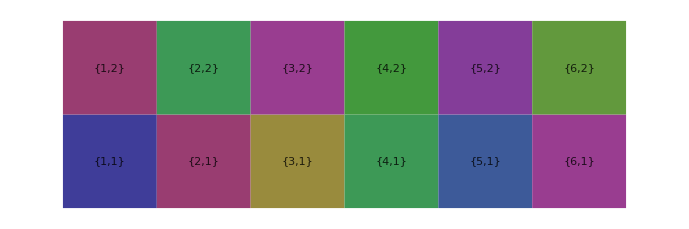

```mathematica
Graphics[CheckerBoardFromList[{0,1,2,3,4,5,6},{0,1,2}]]
```

```mathematica
approxSimplify=Function[{expr},Assuming[Element[m,Integers]&&m>0&&m≤ n&&Element[n,Integers]&&n>3&&Element[θ,Reals]&& θ≥ 0 && θ< Pi&&Element[δθ,Reals]&& δθ≥ 0 && δθ< Pi/6,FullSimplify[expr]]];
```

```mathematica
Format[maxA,TraditionalForm]="(ϕ^⋀)_a";Format[minA,TraditionalForm]="(ϕ^⋁)_a";Format[maxB,TraditionalForm]="(ϕ^⋀)_b";
Format[minB,TraditionalForm]="(ϕ^⋁)_b";Format[extremaA,TraditionalForm]="(ϕ^o)_a";Format[extremaB,TraditionalForm]="(ϕ^o)_b";
Format[interX,TraditionalForm]="ϕ^x";
Format[midM,TraditionalForm]="m̄";
```

```mathematica
ClearAll[extremaA,extremaB]
Format[extremaB[i__],TraditionalForm]:=Row[{"(ϕ^o)_b",Style["("<>Riffle[Map[ToString[#,TraditionalForm]&,{i}],", "]<>")",Small]}];
Format[extremaA[i__],TraditionalForm]:=Row[{"(ϕ^o)_a",Style["("<>Riffle[Map[ToString[#,TraditionalForm]&,{i}],", "]<>")",Small]}] ;
Row[{TraditionalForm[extremaA[5]],"    ",TraditionalForm[extremaB[5]]}]
```

(ϕ^o)_a(TraditionalForm`5)    (ϕ^o)_b(TraditionalForm`5)

## The Points of Intersection.

### Init

```mathematica
δqReFun=Function[{θ6,n},- Round[2^(-3+n) √3 Tan[θ6]]+2^(-3+n) √3 Tan[θ6]];
ClearAll[δqRe]
δqRe[θ:Except[_String],n_]:=δqReFun[Mod[θ,π/6],n];
Format[δqRe, TraditionalForm]=Style["δqRe",Bold];
```

```mathematica
ShowFun[δqRe[θ,n]]
```

δqRe(θ,n) = √3 2^(n-3) tan(θπ/6)-Round[√3 2^(n-3) tan(θπ/6)]

```mathematica
Clear[perterbation,θ]
perterbation[θ:Except[_String],n_]:=Module[{},{{2 δqRe[θ,n],-2 δqRe[θ,n]},{2 δqReFun[Pi/6 -Mod[θ,π/6],n],-2 δqReFun[Pi/6 -Mod[θ,π/6],n]} }];
perterbation[θ_String,n_]:=Module[{},{{2 δqRe[θ,n],-2 δqRe[θ,n]},{2 δqRe["Pi/6 -"<>θ,n],-2 δqRe["Pi/6 -"<>θ,n]} }];
```

```mathematica
TraditionalForm[Row[{perterbation["θ"]," = ",perterbation["θ",n]," = ",perterbation[θ,n]}]]
```

perterbation(θ) = (2 δqRe(θ,n) | -2 δqRe(θ,n)
2 δqRe(Pi/6 -θ,n) | -2 δqRe(Pi/6 -θ,n)) = (2 (2^(n-3) √3 tan(θπ/6)-Round[2^(n-3) √3 tan(θπ/6)]) | -2 (2^(n-3) √3 tan(θπ/6)-Round[2^(n-3) √3 tan(θπ/6)])
2 (2^(n-3) √3 tan(π/6-θπ/6)-Round[2^(n-3) √3 tan(π/6-θπ/6)]) | -2 (2^(n-3) √3 tan(π/6-θπ/6)-Round[2^(n-3) √3 tan(π/6-θπ/6)]))

```mathematica
Block[{i,n,m,θ,y},
thetaIntersectionFun=Function[{m,n},Evaluate[FullSimplify[{θ,Abs[perterbation[θ,n][[1,1]]]}/.θ-> (ArcTan[(-7+2 y+√(49-4 y+4 y^2))/(2 √3)]/.{y-> m 2^(2-n)})]]];
ClearAll[thetaIntersection];
thetaIntersection[m:Except[_String],n_]:=thetaIntersectionFun[m,n];
Format[thetaIntersection, TraditionalForm]=Style["ϕ^x",Bold];
]
```

```mathematica
MatrixForm[ShowFun[thetaIntersection[m,n]]]
```

ϕ^x(m,n) = {tan^-1((m 2^(3-n)+√(49-m 4^(2-n) (2^n-4 m))-7)/(2 √3)),2 Abs[Round[2^(n-3) √3 tan(tan^-1((2^(3-n) m+√(49-4^(2-n) (2^n-4 m) m)-7)/(2 √3))π/6)]-2^(n-3) √3 tan(tan^-1((2^(3-n) m+√(49-4^(2-n) (2^n-4 m) m)-7)/(2 √3))π/6)]}

```mathematica
thetaIntersections=Function[{n}, Table[thetaIntersection[i,n],{i,0,2^(n-2)}]];
```

```mathematica
Block[{i,n,m,θ,y},
θToIndxFun=Function[{θ,n},Evaluate[FullSimplify[i/.Flatten[Solve[θ==thetaIntersection[i,n][[1]],i]]]]];
Clear[θToIndx];
θToIndx[θ:Except[_String],n_]:=θToIndxFun[θ,n];
Format[θToIndx, TraditionalForm]=Style["i",Bold];
];
```

```mathematica
ShowFun[θToIndx[θ,n]]
```

i(θ,n) = (2^(n-3) tan(θ) (√3 tan(θ)+7))/(tan(θ)+√3)

```mathematica
thetaFun=Function[{y},{ArcTan[(√3 y)/(4-y)],ArcTan[y/(√3)]},Listable];
```

#### Minima ϕ^⋁

```mathematica
thetaMinFun=Function[{m,n},Evaluate[Simplify[thetaFun[m  2^(3-n)]]]];
Clear[thetaMin]
thetaMin[m:Except[_String],n:Except[_String]]:=thetaMinFun[m,n];
Format[thetaMin, TraditionalForm]=Style["ϕ^⋁",Bold];
```

```mathematica
ShowFun[thetaMin[m,n]]
```

ϕ^⋁(m,n) = {tan^-1((2 √3 m)/(2^n-2 m)),tan^-1((m 2^(3-n))/(√3))}

```mathematica
thetaMinAFun=Function[{m,n},ArcTan[(2 √3 m)/(2^n-2 m)]];
Clear[thetaMinA]
thetaMinA[m:Except[_String],n:Except[_String]]:=thetaMinAFun[m,n];
Format[thetaMinA, TraditionalForm]=Style["(ϕ^⋁)_a",Bold];
```

```mathematica
ShowFun[thetaMinA[m,n]]
```

(ϕ^⋁)_a(m,n) = tan^-1((2 √3 m)/(2^n-2 m))

```mathematica
thetaMinBFun=Function[{m,n},ArcTan[(2^(3-n) m)/(√3)]];
Clear[thetaMinB]
thetaMinB[m:Except[_String],n:Except[_String]]:=thetaMinBFun[m,n];
Format[thetaMinB, TraditionalForm]=Style["(ϕ^⋁)_b",Bold];
```

```mathematica
ShowFun[thetaMinB[m,n]]
```

(ϕ^⋁)_b(m,n) = tan^-1((m 2^(3-n))/(√3))

#### Maxima ϕ^⋀

```mathematica
thetaMaxFun=Function[{m,n},Evaluate[Simplify[thetaFun[(m +1/2) 2^(3-n)]]]];
Clear[thetaMax]
thetaMax[m:Except[_String],n:Except[_String]]:=thetaMaxFun[m,n];
Format[thetaMax, TraditionalForm]=Style["ϕ^⋀",Bold];
```

```mathematica
ShowFun[thetaMax[m,n]]
```

ϕ^⋀(m,n) = {tan^-1((√3 (2 m+1))/(-2 m+2^n-1)),tan^-1(((2 m+1) 2^(2-n))/(√3))}

```mathematica
thetaMaxAFun=Function[{m,n},ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)]];
Clear[thetaMaxA]
thetaMaxA[m:Except[_String],n:Except[_String]]:=thetaMaxAFun[m,n];
Format[thetaMaxA, TraditionalForm]=Style["(ϕ^⋀)_a",Bold];
```

```mathematica
ShowFun[thetaMaxA[m,n]]
```

(ϕ^⋀)_a(m,n) = tan^-1((√3 (2 m+1))/(-2 m+2^n-1))

```mathematica
thetaMaxBFun=Function[{m,n},ArcTan[(2^(2-n) (1+2 m))/(√3)]];
Clear[thetaMaxB]
thetaMaxB[m:Except[_String],n:Except[_String]]:=thetaMaxBFun[m,n];
Format[thetaMaxB, TraditionalForm]=Style["(ϕ^⋀)_b",Bold];
```

```mathematica
ShowFun[thetaMaxB[m,n]]
```

(ϕ^⋀)_b(m,n) = tan^-1(((2 m+1) 2^(2-n))/(√3))

#### Extrema ϕ^o

```mathematica
thetaExtremaFun=Function[{i,n},Evaluate[Simplify[thetaFun[(i/2) 2^(3-n)]]]];
Clear[thetaExtrema]
thetaExtrema[i:Except[_String],n:Except[_String]]:=thetaExtremaFun[i,n];
Format[thetaExtrema, TraditionalForm]=Style["ϕ^o",Bold];
```

```mathematica
ShowFun[thetaExtrema[m,n]]
```

ϕ^o(m,n) = {tan^-1((√3 m)/(2^n-m)),tan^-1((m 2^(2-n))/(√3))}

```mathematica
thetaExtremaAFun=Function[{i,n},ArcTan[(√3 i)/(2^n-i)]];
Clear[thetaExtremaA];
Format[thetaExtremaA[i__],TraditionalForm]:=Row[{"(ϕ^o)_a",Style["("<>Riffle[Map[ToString[#,TraditionalForm]&,{i}],", "]<>")",Small]}] ;
thetaExtremaA[i:Except[_String],n:Except[_String]]:=thetaExtremaAFun[i,n];
```

```mathematica
ShowFun[thetaExtremaA[i,n]]
```

(ϕ^o)_a(TraditionalForm`"i", TraditionalForm`"n") = tan^-1((√3 i)/(2^n-i))

```mathematica
thetaExtremaBFun=Function[{i,n},ArcTan[(2^(2-n) i)/(√3)]];
Clear[thetaExtremaB];
Format[thetaExtremaB[i__],TraditionalForm]:=Row[{"(ϕ^o)_b",Style["("<>Riffle[Map[ToString[#,TraditionalForm]&,{i}],", "]<>")",Small]}] ;
thetaExtremaB[i:Except[_String],n:Except[_String]]:=thetaExtremaBFun[i,n];
```

```mathematica
ShowFun[thetaExtremaB[i,n]]
```

(ϕ^o)_b(TraditionalForm`"i", TraditionalForm`"n") = tan^-1((i 2^(2-n))/(√3))

#### Misc

```mathematica
midIFun=Function[{n},2^(n-3)];
Clear[midI]
midI[n:Except[_String]]:=midIFun[n];
Format[midI, TraditionalForm]=Style["ī",Bold];
```

```mathematica
ShowFun[midI[n]]
```

ī(n) = 2^(n-3)

```mathematica
thetaFlipEFun=Function[{ι,n},√(2^(2 (n-3))-14 2^(n-3) ι+ ι^2)];
Clear[thetaFlipE]
thetaFlipE[ι:Except[_String],n:Except[_String]]:=thetaFlipEFun[ι,n];
Format[thetaFlipE, TraditionalForm]=Style["Γ",Bold];
```

```mathematica
ShowFun[thetaFlipE[ι,n]]
```

Γ(ι,n) = √(ι^2-7 ι 2^(n-2)+2^(2 (n-3)))

```mathematica
MaxFlips=Function[{n},Floor[N[2^(-3+n) (7-4 √3)]]];
```

```mathematica
indxToθ=Function[{i,n},i 2^(2-n) Pi/6,Listable];
indxFlips=Function[{n},Evaluate[Table[{midI[n]-thetaFlipEFun[ι,n],midI[n]+thetaFlipEFun[ι,n]},{ι,0,MaxFlips[n]}]]];
```

Table::iterb: Iterator {ι, 0, Floor[0.0717968\ 2.^-3. + n]} does not have appropriate bounds.

```mathematica
FlipRegionFun=Function[{i,n},Floor[7 2^(-3+n) -√(49 4^(-3+n)-2^(-2+n) i+i^2)]];
ClearAll[FlipRegion]
Format[FlipRegion[i_,n_], TraditionalForm]:=Style[Subsuperscript["ι",i,n],Bold];
FlipRegion[i:Except[_String],n_]:=FlipRegionFun[i,n];
```

```mathematica
ShowFun[FlipRegion[i,n]]
```

ι_i^n = Floor[7 2^(n-3)-√(i^2-i 2^(n-2)+49 4^(n-3))]

```mathematica
ClearAll[genInterX,genInterXFun]
genInterXFun=Function[{α,β,i,ι,n,oddQI,oddQIota},
If[Xnor[oddQI,oddQIota],
{(α thetaExtremaA[i+ι,n] (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n])+β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n]) thetaExtremaB[i-ι,n])/(β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n])+α (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n])),(α β (thetaExtremaA[i+ι,n]-thetaExtremaB[i-ι,n]))/(β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n])+α (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n]))},
{(β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n]) thetaExtremaB[-1+i-ι,n]+α thetaExtremaA[1+i+ι,n] (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n]))/(β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n])+α (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n])),(α β (-thetaExtremaA[1+i+ι,n]+thetaExtremaB[-1+i-ι,n]))/(β (thetaExtremaA[i+ι,n]-thetaExtremaA[1+i+ι,n])+α (thetaExtremaB[-1+i-ι,n]-thetaExtremaB[i-ι,n]))}
]
];
genInterX[α:Except[_String],β_,i_,ι_,n_]:=Module[{},
genInterXFun[α,β,i,ι,n,OddQ[i],OddQ[ι]]
];
genInterX[α:Except[_String],β_,i_Integer,n_Integer]:=Module[{ι},
ι=FlipRegion[i,n];
genInterXFun[α,β,i,ι,n,OddQ[i],OddQ[ι]]
];
genInterX[α:Except[_String],β_,i:Except[_Integer],n_]:=Module[{ι},
ι=FlipRegion[i,n];
genInterXFun[α,β,i,ι,n,"oddQ"[i],"oddQ"[ι]]
];
Format[genInterX[αβ__,i_,n_],TraditionalForm]:=Row[{Subsuperscript["ϕ^X",i,n],Style["("<>Riffle[Map[ToString[#,TraditionalForm]&,{αβ}],", "]<>")",Small]}]
Format[genInterX[i_,n_],TraditionalForm]:=Row[{Subsuperscript["ϕ^X",i,n]}]
```

```mathematica
ShowFun[genInterX[α,β,"i","n"]]
```

(ϕ^X)_i^n(TraditionalForm`"\[Alpha]", TraditionalForm`"\[Beta]") = If[oddQ(i)\[Xnor]oddQ(ι_i^n),{(α (ϕ^o)_a(TraditionalForm`, TraditionalForm`"n") ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n"))+β (ϕ^o)_b(TraditionalForm`, TraditionalForm`"n") ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")))/(β ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n"))+α ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n"))),(α β ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")))/(β ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n"))+α ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")))},{(α (ϕ^o)_a(TraditionalForm`, TraditionalForm`"n") ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n"))+β (ϕ^o)_b(TraditionalForm`, TraditionalForm`"n") ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")))/(β ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n"))+α ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n"))),(α β ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")))/(β ((ϕ^o)_a(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_a(TraditionalForm`, TraditionalForm`"n"))+α ((ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")-(ϕ^o)_b(TraditionalForm`, TraditionalForm`"n")))}]

```mathematica
ClearAll[extremaA,extremaB]
Format[extremaB[i_],TraditionalForm]:=Row[{"(ϕ^o)_b",Style["("<>ToString[i,TraditionalForm]<>")",Small]}];
Format[extremaA[i_],TraditionalForm]:=Row[{"(ϕ^o)_a",Style["("<>ToString[i,TraditionalForm]<>")",Small]}] ;
Row[{TraditionalForm[extremaA[5]],"    ",TraditionalForm[extremaB[5]]}]
```

(ϕ^o)_a(TraditionalForm`5)    (ϕ^o)_b(TraditionalForm`5)

```mathematica
perterbationLegend[colors_]:=Module[{},
If[Length[colors]>2,
SwatchLegend[colors, Map[TraditionalForm,{"2 δqRe"["δθ"],"-2 δqRe"["δθ"],"2 δqRe"[Pi/6 -"δθ"],"-2 δqRe"[Pi/6 -"δθ"]}] ],
SwatchLegend[colors, Map[TraditionalForm,{"±2 δqRe"["δθ"],"±2 δqRe"[Pi/6 -"δθ"]}] ]
]]
```

```mathematica
Clear[perturbationPlot];
Options[perturbationPlot]={PlotRange-> {0,Pi/6}};
perturbationPlot[theta_,τ_:0.5,n_:8, αβ:{_, _}:{1,1},OptionsPattern[]]:=Module[{pltRange,indxRange,minAf,minBf,maxAf,maxBf,pts,bColor=Green,aColor=Red,δθ,Θ,
maxAs,minAs,maxBs,minBs,pntA,pntB,interXs,interXPts,boundarys,ThetaBoundarys,iota,iotaBg,ϕTicks,title,selectX,selectXindx,selectXindxPrint,selectXTable,plt,valTable},
δθ=Mod[theta,Pi/6]; 
Θ=Quotient[theta,Pi/6] Pi/6;
pltRange=OptionValue[PlotRange];
indxRange={Ceiling[N[θToIndx[pltRange[[1]],n]]],Floor[N[θToIndx[pltRange[[2]],n]]]};
maxAs=Table[{pntLabel[{thetaExtremaA[i,n],αβ[[2]]},extremaA[i],{0,1}, aColor], pntLabel[{thetaExtremaA[i,n],-αβ[[2]]},extremaA[i],{0,1}, aColor]}, {i,1,2^(n-2)-1,2}];
minAs=Table[ pntLabel[{thetaExtremaA[i,n],0},extremaA[i],{0,1}, aColor], {i,2,2^(n-2)-1,2}];
maxBs=Table[{pntLabel[{thetaExtremaB[i,n],αβ[[1]]},extremaB[i],{0,-1}, bColor], pntLabel[{thetaExtremaB[i,n],-αβ[[1]]},extremaB[i],{0,-1}, bColor]}, {i,1,2^(n-2)-1,2}];
minBs=Table[ pntLabel[{thetaExtremaB[i,n],0},extremaB[i],{0,-1}, bColor], {i,2,2^(n-2)-1,2}];
If[αβ=={1,1},
interXPts=Table[thetaIntersection[i,n],{i,indxRange[[1]],indxRange[[2]],1}];
interXs=Table[pntA=interXPts[[i]]; pntB={1,-1}interXPts[[i]]; ii=i+indxRange[[1]]-1;{
pntLabel[pntA,thetaIntersection[ii],If[pntA[[2]]< τ,{0,-1},{0,1}],If[pntA[[2]]< τ,RGBColor[1/3,1/3,1,1],Darker[Blue]],If[pntA[[2]]< τ,RGBColor[1,1,1,0.6],RGBColor[2/3,2/3,1,0]]],
pntLabel[pntB,thetaIntersection[ii],If[pntB[[2]]<-τ,{0,-1},{0,1}],If[pntB[[2]]>-τ,RGBColor[1/3,1/3,1,1],Darker[Blue]],If[pntB[[2]]>-τ,RGBColor[1,1,1,0.6],RGBColor[2/3,2/3,1,0]]]}
,{i,1,Length[interXPts],1}];
,
interXPts=Table[genInterX[αβ[[1]],αβ[[2]],i,n],{i,indxRange[[1]],indxRange[[2]],1}];
 interXs=Table[pntA=interXPts[[i]]; pntB={1,-1}interXPts[[i]]; ii=i+indxRange[[1]]-1;
 {pntLabel[pntA,genInterX[ii,n],If[pntA[[2]]< τ,{0,-1},{0,1}],If[pntA[[2]]< τ,RGBColor[1/3,1/3,1,1],Darker[Blue]],If[pntA[[2]]< τ,RGBColor[1,1,1,0.6],RGBColor[2/3,2/3,1,0]]]
 ,pntLabel[pntB,genInterX[ii,n],If[pntB[[2]]<-τ,{0,-1},{0,1}],If[pntB[[2]]>-τ,RGBColor[1/3,1/3,1,1],Darker[Blue]],If[pntB[[2]]>-τ,RGBColor[1,1,1,0.6],RGBColor[2/3,2/3,1,0]]]
},{i,1,Length[interXPts],1}];
];
boundarys=Sort[Flatten[N[indxFlips[n]]]];
ThetaBoundarys=Evaluate[indxToθ[boundarys,n]];
iota=Flatten[{Table[ι,{ι,0,MaxFlips[n]}],Table[ι,{ι,MaxFlips[n]-1,0,-1}]}];
iotaBg=CheckerBoardFromList[ThetaBoundarys,{-Max[αβ],Max[αβ]}, 
         Table[ColorData[1][iota[[i]]],{i,1,Length[ThetaBoundarys]-1,1},{j,1,1,1}],
         Table[Row[{"ι = ",iota[[i]]}],{i,1,Length[ThetaBoundarys]-1,1},{j,1,1,1}], {0,-1}, 0.9];
ϕTicks=ReleaseHold[Table[
If[thetaIntersection[i,n][[2]]≤1,{N[thetaIntersection[i,n][[1]]],TraditionalForm[thetaIntersection[i]]},Hold[Sequence[]]]
,{i,0,2^(n-2),1}]];
title=Column[{Row[{"Perturbation to channels a and b against angle δθ"}], Row[{"For n =",n,"  with ι regions shaded and extrema labeled"}]}];
selectX=Select[interXPts,(#[[2]]<τ)&];
selectXindx=Map[(Round[N[θToIndx[#[[1]],n]]])&,selectX];
selectXindxPrint = Map[TraditionalForm[thetaIntersection[#]]&,selectXindx];
selectXTable=Panel[TableForm[Transpose[{
  Map[NumberForm[N[(#+Θ)],{4,4}] &,selectX[[All,1]]],
  Map[("±"<>ToString[NumberForm[#,{4,4}]])&,N[selectX[[All,2]]]],
  Map[ToString[NumberForm[N[(#-Mod[theta,Pi/6]) 180/Pi],{4,4},NumberSigns->{"-","+"}]]<>"°"&,selectX[[All,1]]]}],
  TableHeadings->{selectXindxPrint,{"θ'","Perturbation","Change in θ"}},TableAlignments->Center],"Values of θ which produce a perturbation less than τ"];
valTable=Column[{
Panel[Row[{Grid[{{"θ","Θ","δθ","τ"},{NumberForm[theta,{4,4}],Θ,NumberForm[δθ,{4,4}],τ}},Frame->All]}],"θ = Θ + δθ"],
Panel[Row[{ToString[NumberForm[N[(pltRange[[1]]) 180/Pi],{2,2},NumberSigns->{"-","+"}]]<>"°"," < ","θ'"," < ",ToString[NumberForm[N[(pltRange[[2]]) 180/Pi],{2,2},NumberSigns->{"-","+"}]]<>"°"}],"Acceptable Values for θ'"],
selectXTable}];
plt=Plot[Evaluate[Flatten[αβ perterbation[θ,n]]],{θ,pltRange[[1]],pltRange[[2]]},
  PlotStyle->{ bColor,Darker[ bColor], aColor,Darker[ aColor]}, 
  PlotLabel-> title,Frame->True,FrameLabel->{{"Perturbation",None},{"δθ",None}},
  FrameTicks->{{FracTicks[-2,2,2],{{τ,"τ"},{-τ,"-τ"}}},{Append[PiTicks[pltRange[[1]],pltRange[[2]],8],{δθ,"δθ",{0.01,0},-Graphics-}],ReleaseHold[Table[Hold[Sequence][{(ThetaBoundarys[[i]]+ThetaBoundarys[[i-1]])/2,Row[{"ι = ",i-2}] },ThetaBoundarys[[i]] ],{i,2,Length[ThetaBoundarys]}]]}},
  Epilog->Flatten[{maxBs,minBs,maxAs,minAs,interXs,Black,Inset[Panel[perterbationLegend[{bColor, aColor}],Background->Opacity[0.7,White]],Scaled[{.95,.1}],{Right,Bottom}]}]];
Grid[{{Show[{plt,Graphics[maxBs],Graphics[{Opacity[0.5],iotaBg}],plt,Graphics[{Opacity[1],Black,Line[{{δθ,-Max[αβ]-0.3},{δθ,Max[αβ]+0.3}}],Line[{{pltRange[[1]],-τ},{pltRange[[2]],-τ}}],Line[{{pltRange[[1]],τ},{pltRange[[2]],τ}}]}]}],valTable}},Alignment->{Left,Top}]
]
```

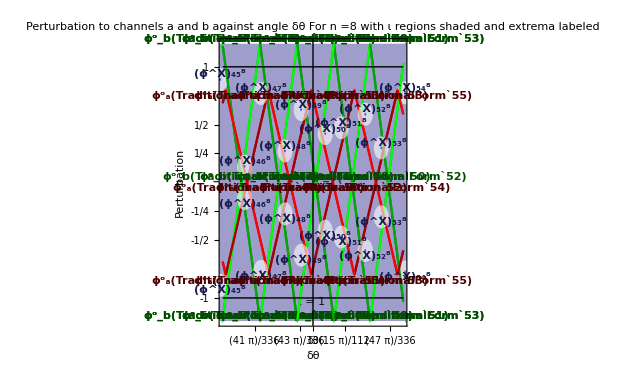
-Graphics- | θ | Θ | δθ | τ
0.9312 | π/6 | 0.4076 | 1θ = Θ + δθ
+21.00° < θ' < +25.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(45) | 0.8928 | ±0.8904 | -2.2000°
ϕ^x(46) | 0.9028 | ±0.1404 | -1.6240°
ϕ^x(47) | 0.9095 | ±0.7691 | -1.2400°
ϕ^x(48) | 0.9196 | ±0.2723 | -0.6648°
ϕ^x(49) | 0.9262 | ±0.6300 | -0.2820°
ϕ^x(50) | 0.9362 | ±0.4221 | +0.2907°
ϕ^x(51) | 0.9429 | ±0.4730 | +0.6718°
ϕ^x(52) | 0.9528 | ±0.5897 | +1.2420°
ϕ^x(53) | 0.9595 | ±0.2981 | +1.6210°
ϕ^x(54) | 0.9694 | ±0.7752 | +2.1890°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[θp,1,8,{1.2,0.8},PlotRange->{Mod[θp,Pi/6]-(Pi/84),Mod[θp,Pi/6] + (Pi/84)}]
```

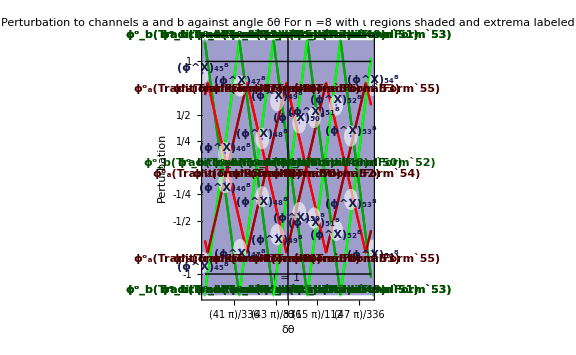
-Graphics- | θ | Θ | δθ | τ
0.9312 | π/6 | 0.4076 | 1θ = Θ + δθ
+21.00° < θ' < +25.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(45) | 0.8928 | ±0.8904 | -2.2000°
ϕ^x(46) | 0.9028 | ±0.1404 | -1.6240°
ϕ^x(47) | 0.9095 | ±0.7691 | -1.2400°
ϕ^x(48) | 0.9196 | ±0.2723 | -0.6648°
ϕ^x(49) | 0.9262 | ±0.6300 | -0.2820°
ϕ^x(50) | 0.9362 | ±0.4221 | +0.2907°
ϕ^x(51) | 0.9429 | ±0.4730 | +0.6718°
ϕ^x(52) | 0.9528 | ±0.5897 | +1.2420°
ϕ^x(53) | 0.9595 | ±0.2981 | +1.6210°
ϕ^x(54) | 0.9694 | ±0.7752 | +2.1890°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[θp,1,8,{1.2,0.8},PlotRange->{Mod[θp,Pi/6]-(Pi/84),Mod[θp,Pi/6] + (Pi/84)}]
```

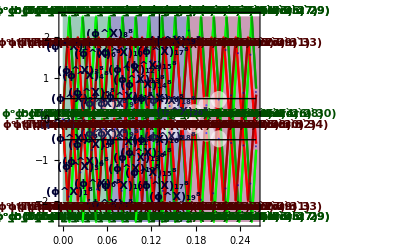
-Graphics- | θ | Θ | δθ | τ
0.6545 | π/6 | 0.1309 | 1/2θ = Θ + δθ
+0.00° < θ' < +15.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(0) | 0.5236 | ±0.0000 | -7.5000°
ϕ^x(7) | 0.5787 | ±0.2365 | -4.3410°
ϕ^x(9) | 0.5946 | ±0.2361 | -3.4330°
ϕ^x(18) | 0.6684 | ±0.3186 | +0.7938°
ϕ^x(20) | 0.6848 | ±0.0598 | +1.7380°
ϕ^x(22) | 0.7014 | ±0.1591 | +2.6880°
ϕ^x(24) | 0.7180 | ±0.3385 | +3.6410°
ϕ^x(26) | 0.7347 | ±0.4785 | +4.5980°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[N[Pi/6+Pi/24],1/2,8,{2.5,2},PlotRange->{0,Pi/12}]
```

### Functions

Two perturbation legend styles are available.

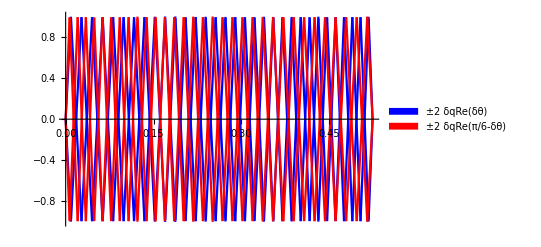

```mathematica
Plot[Evaluate[Flatten[perterbation[θ,8]]],{θ,0,Pi/6},PlotStyle->{Blue,Blue,Red,Red},PlotLegends->Panel@perterbationLegend[{Blue,Red}]]
```

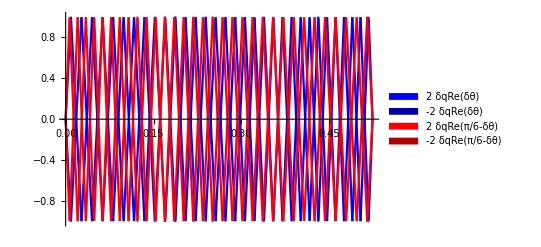

```mathematica
Plot[Evaluate[Flatten[perterbation[θ,8]]],{θ,0,Pi/6},PlotStyle->{Blue,Blue,Red,Red},PlotLegends->Panel[perterbationLegend[{Blue,Darker[Blue],Red,Darker[Red]}]]]
```

The intersection at index i and data type depth n

```mathematica
Row[{TraditionalForm[interX[i,n]]," = ",MatrixForm[{TraditionalForm@thetaIntersection[i,n][[1]],TraditionalForm@thetaIntersection[i,n][[2]]}]}]
```

ϕ^x(i,n) = (tan^-1((√(i^2 2^(6-2 n)-i 2^(4-n)+49)+i 2^(3-n)-7)/(2 √3))
{2 Abs[2^(n-3) √3 tan(tan^-1((2^(3-n) i+√(2^(6-2 n) i^2-2^(4-n) i+49)-7)/(2 √3))π/6)-Round[2^(n-3) √3 tan(tan^-1((2^(3-n) i+√(2^(6-2 n) i^2-2^(4-n) i+49)-7)/(2 √3))π/6)]],2 Abs[2^(n-3) √3 tan(tan^-1((2^(3-n) i+√(2^(6-2 n) i^2-2^(4-n) i+49)-7)/(2 √3))π/6)-Round[2^(n-3) √3 tan(tan^-1((2^(3-n) i+√(2^(6-2 n) i^2-2^(4-n) i+49)-7)/(2 √3))π/6)]]})

## The Extrema in order.

### Init

### Development

The inverse function finds points out of order

```mathematica
thetaFun=Function[{y},{ArcTan[(√3 (1-y))/(3+y)],ArcTan[y/(√3)]},Listable];
```

```mathematica
distinctErrorFunc[θ,n,Round]
```

{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]-2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]],-4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}}

```mathematica
TraditionalForm@perterbation[θ,n]
```

(2 (2^(n-3) √3 tan(θπ/6)-Round[2^(n-3) √3 tan(θπ/6)]) | -2 (2^(n-3) √3 tan(θπ/6)-Round[2^(n-3) √3 tan(θπ/6)])
2 (2^(n-3) √3 tan((π/6-θπ/6)π/6)-Round[2^(n-3) √3 tan((π/6-θπ/6)π/6)]) | -2 (2^(n-3) √3 tan((π/6-θπ/6)π/6)-Round[2^(n-3) √3 tan((π/6-θπ/6)π/6)]))

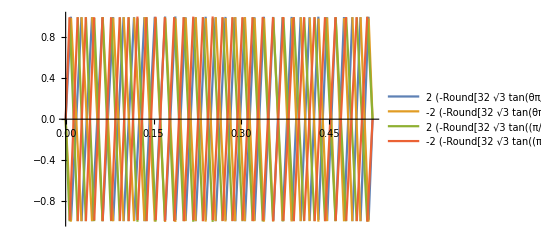

```mathematica
Plot[Evaluate[Flatten[perterbation[θ,8]]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

```mathematica
Block[{n=8},
Table[
thetaFun[m 2^(3-n)],{m,0,2^(n-3)}]
]
```

{{π/6,0},{ArcTan[(31 √3)/97],ArcTan[1/(32 √3)]},{ArcTan[(15 √3)/49],ArcTan[1/(16 √3)]},{ArcTan[29/(33 √3)],ArcTan[(√3)/32]},{ArcTan[(7 √3)/25],ArcTan[1/(8 √3)]},{ArcTan[(27 √3)/101],ArcTan[5/(32 √3)]},{ArcTan[13/(17 √3)],ArcTan[(√3)/16]},{ArcTan[(25 √3)/103],ArcTan[7/(32 √3)]},{ArcTan[(3 √3)/13],ArcTan[1/(4 √3)]},{ArcTan[23/(35 √3)],ArcTan[(3 √3)/32]},{ArcTan[(11 √3)/53],ArcTan[5/(16 √3)]},{ArcTan[(21 √3)/107],ArcTan[11/(32 √3)]},{ArcTan[5/(9 √3)],ArcTan[(√3)/8]},{ArcTan[(19 √3)/109],ArcTan[13/(32 √3)]},{ArcTan[(9 √3)/55],ArcTan[7/(16 √3)]},{ArcTan[17/(37 √3)],ArcTan[(5 √3)/32]},{ArcTan[(√3)/7],ArcTan[1/(2 √3)]},{ArcTan[(15 √3)/113],ArcTan[17/(32 √3)]},{ArcTan[7/(19 √3)],ArcTan[(3 √3)/16]},{ArcTan[(13 √3)/115],ArcTan[19/(32 √3)]},{ArcTan[(3 √3)/29],ArcTan[5/(8 √3)]},{ArcTan[11/(39 √3)],ArcTan[(7 √3)/32]},{ArcTan[(5 √3)/59],ArcTan[11/(16 √3)]},{ArcTan[(9 √3)/119],ArcTan[23/(32 √3)]},{ArcTan[1/(5 √3)],ArcTan[(√3)/4]},{ArcTan[(7 √3)/121],ArcTan[25/(32 √3)]},{ArcTan[(3 √3)/61],ArcTan[13/(16 √3)]},{ArcTan[5/(41 √3)],ArcTan[(9 √3)/32]},{ArcTan[(√3)/31],ArcTan[7/(8 √3)]},{ArcTan[(3 √3)/125],ArcTan[29/(32 √3)]},{ArcTan[1/(21 √3)],ArcTan[(5 √3)/16]},{ArcTan[(√3)/127],ArcTan[31/(32 √3)]},{0,π/6}}

```mathematica
Simplify[thetaFun[(1-y)]]
```

{ArcTan[(√3 y)/(4-y)],ArcTan[(1-y)/(√3)]}

The functions are now in the correct order

```mathematica
Row[{"thetaFun[y]=",thetaFun[y]}]
Row[{"thetaMin[y]=",thetaMin[m,n]}]
Row[{"thetaMax[y]=",thetaMax[m,n]}]
Row[{"thetaExtrema[y]=",thetaExtrema[i,n]}]
```

thetaFun[y]={ArcTan[(√3 y)/(4-y)],ArcTan[y/(√3)]}

thetaMin[y]={ArcTan[(2 √3 m)/(2^n-2 m)],ArcTan[(2^(3-n) m)/(√3)]}

thetaMax[y]={ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)],ArcTan[(2^(2-n) (1+2 m))/(√3)]}

thetaExtrema[y]={ArcTan[(√3 i)/(2^n-i)],ArcTan[(2^(2-n) i)/(√3)]}

```mathematica
Clear[m,n];
Grid[{{TraditionalForm[minA]," = ",thetaMin[m,n][[1]],"  with   m = { 0,1,2,3 ... 2^(n - 3) }"  },
{TraditionalForm[minB]," = ",thetaMin[m,n][[2]],"  with   m = { 0,1,2,3 ... 2^(n - 3) }"},
{TraditionalForm[maxA]," = ",thetaMax[m,n][[1]],"  with   m = { 0,1,2,3 ... 2^(n - 3)-1 }"},
{TraditionalForm[maxB]," = ",thetaMax[m,n][[2]],"  with   m = { 0,1,2,3 ... 2^(n - 3)-1 }"},
{TraditionalForm[extremaA]," = ",thetaExtrema[i,n][[1]],"  with   i = { 0,1,2,3 ... 2^(n - 2) }"},
{TraditionalForm[extremaB]," = ",thetaExtrema[i,n][[2]],"  with   i = { 0,1,2,3 ... 2^(n - 2) }"}}]
```

(ϕ^⋁)_a |  =  | ArcTan[(2 √3 m)/(2^n-2 m)] |   with   m = { 0,1,2,3 ... 2^(n - 3) }
(ϕ^⋁)_b |  =  | ArcTan[(2^(3-n) m)/(√3)] |   with   m = { 0,1,2,3 ... 2^(n - 3) }
(ϕ^⋀)_a |  =  | ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)] |   with   m = { 0,1,2,3 ... 2^(n - 3)-1 }
(ϕ^⋀)_b |  =  | ArcTan[(2^(2-n) (1+2 m))/(√3)] |   with   m = { 0,1,2,3 ... 2^(n - 3)-1 }
(ϕ^o)_a |  =  | ArcTan[(√3 i)/(2^n-i)] |   with   i = { 0,1,2,3 ... 2^(n - 2) }
(ϕ^o)_b |  =  | ArcTan[(2^(2-n) i)/(√3)] |   with   i = { 0,1,2,3 ... 2^(n - 2) }

#### Extrema ordering swaps

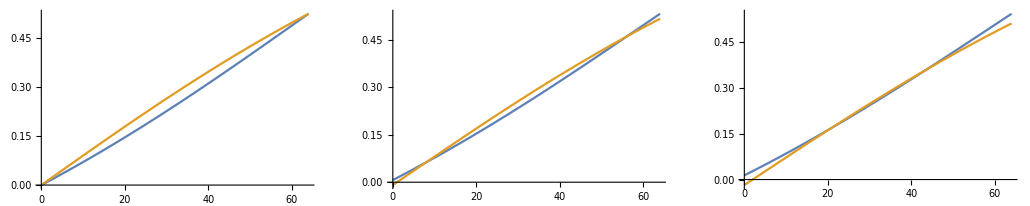

```mathematica
Block[{n=8},
extremaAf=Function[{i},Evaluate[thetaExtrema[i,n][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,n][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,n][[1]]]];GraphicsRow[{Plot[{extremaAf[i],extremaBf[i]},{i,0,2^(n-2)}],Plot[{extremaAf[i+1],extremaBf[i-1]},{i,0,2^(n-2)}],Plot[{extremaAf[i+2],extremaBf[i-2]},{i,0,2^(n-2)}]}]]
```

```mathematica
N[Solve[extremaAf[i+1]==extremaBf[i-1],i]/.n->8]
N[Solve[extremaAf[i+2]==extremaBf[i-2],i]/.n->8]
N[Solve[extremaAf[i+3]==extremaBf[i-3],i]/.n->8]
```

{{i→7.97918},{i→56.0208}}

{{i→20.5109},{i→43.4891}}

{{i→32.-17.6352 ⅈ},{i→32.+17.6352 ⅈ}}

```mathematica
FullSimplify[i/.Solve[extremaAf[i+1]==extremaBf[i-1],i]]
FullSimplify[i/.Solve[extremaAf[i+2]==extremaBf[i-2],i]]
```

{1/8 (2^n-√(64-7 2^(4+n)+4^n)),1/8 (2^n+√(64-7 2^(4+n)+4^n))}

{1/8 (2^n-√(256-7 2^(5+n)+4^n)),1/8 (2^n+√(256-7 2^(5+n)+4^n))}

```mathematica
FullSimplify[i/.Solve[extremaAf[i+ι]==extremaBf[i-ι],i]]
ExpandAll[%]
```

{1/8 (2^n-√(4^n-7 2^(4+n) ι+64 ι^2)),1/8 (2^n+√(4^n-7 2^(4+n) ι+64 ι^2))}

{2^(-3+n)-1/8 √(2^(2 n)-7 2^(4+n) ι+64 ι^2),2^(-3+n)+1/8 √(2^(2 n)-7 2^(4+n) ι+64 ι^2)}

```mathematica
{2^(-3+n)- √(2^(2 (n-3))-14 2^(n-3) ι+ ι^2),2^(-3+n)+ √(2^(2 (n-3))-14 2^(n-3) ι+ ι^2)}
```

```mathematica
ShowFun[midI[n]]
```

```mathematica
ShowFun[thetaFlipE[ι,n]]
```

```mathematica
Column[{
TraditionalForm[Row[{midI[n]," = ",midI[n]}]],
TraditionalForm[Row[{thetaFlipE[ι,n]," = ",thetaFlipEFun[ι,n]}]],
"The peak ordering changes in each region ",
TraditionalForm[midI[n]-thetaFlipE[ι,n]≤i≤midI[n]+thetaFlipE[ι,n]]
}]
```

ī(n) = 2^(n-3)
Γ(ι,n) = √(ι^2-7 ι 2^(n-2)+2^(2 (n-3)))
The peak ordering changes in each region 
ī(n)-Γ(ι,n)≤i≤Γ(ι,n)+ī(n)

The number of regions depends on n

```mathematica
Assuming[ι∈Reals&&1<ι<2^(n-2)&&n∈Integers&&n>3,FullSimplify[Reduce[
Evaluate[thetaFlipEFun[ι,n][[1]]]≥0 
&& ι∈Reals&&ι>1&&n∈Integers&&n>3,ι]]]
```

n≥7&&ι≤2^(-3+n) (7-4 √3)

```mathematica
Definition[MaxFlips]
```

MaxFlips=Function[{n},Floor[N[2^(-3+n) (7-4 √3)]]]

```mathematica
MaxFlips=Function[{n},Floor[2^(-3+n) (7-4 √3)]];
```

```mathematica
Table[{n,MaxFlips[n]},{n,3,32}]
```

{{3,0},{4,0},{5,0},{6,0},{7,1},{8,2},{9,4},{10,9},{11,18},{12,36},{13,73},{14,147},{15,294},{16,588},{17,1176},{18,2352},{19,4705},{20,9410},{21,18821},{22,37642},{23,75284},{24,150568},{25,301137},{26,602274},{27,1204549},{28,2409099},{29,4818199},{30,9636399},{31,19272798},{32,38545597}}

given i what region ι are we in?

```mathematica
Assuming[ι∈Reals&&1<ι<2^(n-2)&&n∈Integers&&n>3,FullSimplify[Reduce[
(i-midI[n])==thetaFlipEFun[ι,n]&& ι∈Reals&&ι>1&&n∈Integers&&n>3,ι]]]
```

Reduce[-2^(-3+n)+i==√(2^(2 (-3+n))-7 2^(-2+n) ι+ι^2)&&ι∈Reals&&ι>1&&n∈Integers&&n>3,ι]

```mathematica
indxToθ=Function[{i,n},i 2^(2-n) Pi/6,Listable];
indxFlips=Function[{n},Evaluate[Table[{midI[n]-thetaFlipEFun[ι,n],midI[n]+thetaFlipEFun[ι,n]},{ι,0,MaxFlips[n]}]]];
```

Table::iterb: Iterator {ι, 0, Floor[2^-3 + n\ (7 - 4\ √3)]} does not have appropriate bounds.

```mathematica
ι
```

ι

```mathematica
indxFlips
```

```mathematica
Function[{n},Table[{midI[n]-thetaFlipEFun[ι,n],midI[n]+thetaFlipEFun[ι,n]},{ι,0,Floor[2^(-3+n) (7-4 √3)]}]]
```

```mathematica
distinctErrorFunc
```

Function[{θ,n,round},{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{-4 Round[2^(-2+n) Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]]]+2^n Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]],-4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}}]

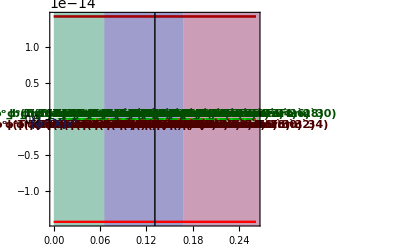
-Graphics- | θ | Θ | δθ | τ
0.6545 | π/6 | 0.1309 | 1/4θ = Θ + δθ
+0.00° < θ' < +15.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(0) | 0.5236 | ±0.0000 | -7.5000°
ϕ^x(7) | 0.5786 | ±0.2156 | -4.3460°
ϕ^x(9) | 0.5947 | ±0.2149 | -3.4270°
ϕ^x(20) | 0.6848 | ±0.0542 | +1.7370°
ϕ^x(22) | 0.7015 | ±0.1439 | +2.6910°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[N[Pi/6+Pi/24],1/4,8,{2,2},PlotRange->{0,Pi/12}]
```

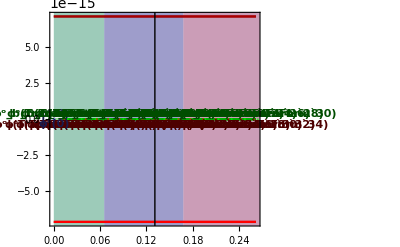
-Graphics- | θ | Θ | δθ | τ
0.6545 | π/6 | 0.1309 | 1/4θ = Θ + δθ
+0.00° < θ' < +15.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(0) | 0.5236 | ±0.0000 | -7.5000°
ϕ^x(7) | 0.5786 | ±0.1076 | -4.3460°
ϕ^x(9) | 0.5947 | ±0.1076 | -3.4280°
ϕ^x(18) | 0.6682 | ±0.1441 | +0.7862°
ϕ^x(20) | 0.6848 | ±0.0270 | +1.7370°
ϕ^x(22) | 0.7015 | ±0.0721 | +2.6910°
ϕ^x(24) | 0.7182 | ±0.1532 | +3.6490°
ϕ^x(26) | 0.7349 | ±0.2163 | +4.6100°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[N[Pi/6+Pi/24],1/4,8,{1,1},PlotRange->{0,Pi/12}]
```

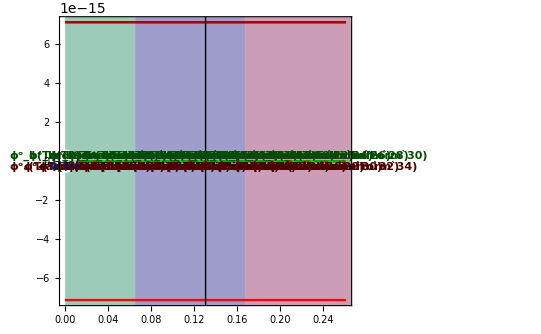
-Graphics- | θ | Θ | δθ | τ
0.6545 | π/6 | 0.1309 | 1/4θ = Θ + δθ
+0.00° < θ' < +15.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(0) | 0.5236 | ±0.0000 | -7.5000°
ϕ^x(7) | 0.5786 | ±0.1076 | -4.3460°
ϕ^x(9) | 0.5947 | ±0.1076 | -3.4280°
ϕ^x(18) | 0.6682 | ±0.1441 | +0.7862°
ϕ^x(20) | 0.6848 | ±0.0270 | +1.7370°
ϕ^x(22) | 0.7015 | ±0.0721 | +2.6910°
ϕ^x(24) | 0.7182 | ±0.1532 | +3.6490°
ϕ^x(26) | 0.7349 | ±0.2163 | +4.6100°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[N[Pi/6+Pi/24],1/4,8,PlotRange->{0,Pi/12}]
```

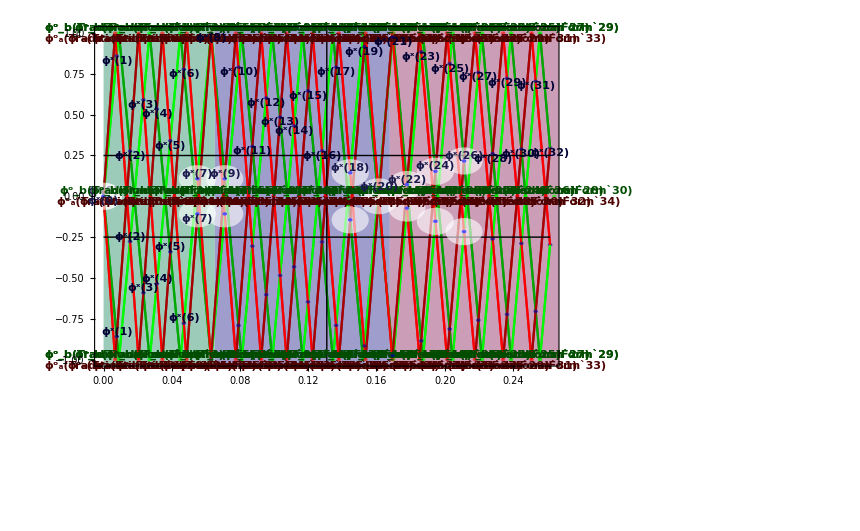
-Graphics- | θ | Θ | δθ | τ
0.6545 | π/6 | 0.1309 | 1/4θ = Θ + δθ
+0.00° < θ' < +15.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(0) | 0.5236 | ±0.0000 | -7.5000°
ϕ^x(7) | 0.5786 | ±0.1076 | -4.3460°
ϕ^x(9) | 0.5947 | ±0.1076 | -3.4280°
ϕ^x(18) | 0.6682 | ±0.1441 | +0.7862°
ϕ^x(20) | 0.6848 | ±0.0270 | +1.7370°
ϕ^x(22) | 0.7015 | ±0.0721 | +2.6910°
ϕ^x(24) | 0.7182 | ±0.1532 | +3.6490°
ϕ^x(26) | 0.7349 | ±0.2163 | +4.6100°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[N[Pi/6+Pi/24],1/4,8,PlotRange->{0,Pi/12}]
```

```mathematica
Block[{minAf,minBf,maxAf,maxBf,n=8,pts,bColor=Green,aColor=Red},
extremaAf=Function[{i},Evaluate[thetaExtrema[i,n][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,n][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,n][[1]]]];
;
maxBs=Table[
 {pntLabel[{extremaBf[i],1},extremaB[i],{0,-1}, bColor],pntLabel[{extremaBf[i],-1},extremaB[i],{0,-1}, bColor]}
,{i,1,2^(n-2)-1,2}];
minBs=Table[
 pntLabel[{extremaBf[i],0},extremaB[i],{0,-1}, bColor]
,{i,2,2^(n-2)-1,2}];
maxAs=Table[
{ pntLabel[{extremaAf[i],1},extremaA[i],{0,1}, aColor],pntLabel[{extremaAf[i],-1},extremaA[i],{0,1}, aColor]}
,{i,1,2^(n-2)-1,2}];
minAs=Table[
 pntLabel[{extremaAf[i],0},extremaA[i],{0,1}, aColor]
,{i,2,2^(n-2)-1,2}];
interXs=Table[pnt=thetaIntersection[i,n];
 pntLabel[pnt,interX[i],If[pnt[[2]]<1/2,{0,-1},{0,1}],If[pnt[[2]]<1/2,Blue,Darker[Blue]]]
,{i,2,2^(n-2)-1,1}];
interXs2=Table[pnt={1,-1} thetaIntersection[i,n];
 pntLabel[pnt,interX[i],If[pnt[[2]]<-1/2,{0,-1},{0,1}],If[pnt[[2]]<-1/2,Blue,Darker[Blue]]]
,{i,2,2^(n-2)-1,1}];
boundarys=Sort[Flatten[N[indxFlips[n]]]];
ThetaBoundarys=Evaluate[indxToθ[boundarys,n]];
iota=Flatten[{Table[ι,{ι,0,MaxFlips[n]}],Table[ι,{ι,MaxFlips[n]-1,0,-1}]}];
iotaBg=CheckerBoardFromList[ThetaBoundarys,{-2,2},
Table[ColorData[1][iota[[i]]],{i,1,Length[ThetaBoundarys]-1,1},{j,1,1,1}],
Table[Row[{"ι = ",iota[[i]]}],{i,1,Length[ThetaBoundarys]-1,1},{j,1,1,1}]
,{0,-1},0.9];
ϕTicks=ReleaseHold[Table[
If[thetaIntersection[i,n][[2]]≤1,{N[interXf[i]],TraditionalForm[interX[i]]},Hold[Sequence[]]]
,{i,0,2^(n-2),1}]];
title=Column[{Row[{"Perturbation to channels a and b against angle δθ"}], Row[{"For n =",n,"  with ι regions shaded and extrema labeled"}]}];
plt=Plot[Evaluate[Flatten[perterbation[θ,n]]],{θ,0,Pi/12},PlotStyle->{ bColor,Darker[ bColor], aColor,Darker[ aColor]}, PlotLabel-> None,Frame->True,FrameLabel->{{"Perturbation",None},{"θ",None}},FrameTicks->{{FracTicks[-2,2,2],None},{PiTicks[0,Pi/12,8],ReleaseHold[Table[Hold[Sequence][{(ThetaBoundarys[[i]]+ThetaBoundarys[[i-1]])/2,Row[{"ι = ",i-2}] },ThetaBoundarys[[i]] ],{i,2,Length[ThetaBoundarys]}]]}},Epilog->Flatten[{maxBs,minBs,maxAs,minAs,interXs,interXs2,Black,Inset[Panel[perterbationLegend[{bColor, aColor}],Background->Opacity[0.7,White]],Scaled[{.95,.1}],{Right,Bottom}]}]];
Show[{plt,Graphics[{Opacity[0.5],iotaBg}],plt}]

]
```

-Graphics-

```mathematica
Block[{n=8},boundarys=Sort[Flatten[N[indxFlips[n]]]];
indxToθ[boundarys,n]]
```

{0.,0.0652795,0.167804,0.355795,0.458319,0.523599}

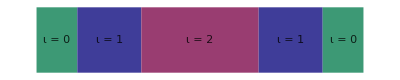

```mathematica
Block[{n=8},
boundarys=Sort[Flatten[N[indxFlips[8]]]];
iota=Flatten[{Table[ι,{ι,0,MaxFlips[8]}],Table[ι,{ι,MaxFlips[8]-1,0,-1}]}];
Graphics[CheckerBoardFromList[boundarys,{0,2},
Table[ColorData[1][iota[[i]]],{i,1,Length[boundarys]-1,1},{j,1,1,1}],
Table[Row[{"ι = ",iota[[i]]}],{i,1,Length[boundarys]-1,1},{j,1,1,1}]
,{0,0},0.9]]
]
```

```mathematica
(-2^(-3+n)+i)^2==2^(2 (-3+n))-7 2^(-2+n) ι+ι^2
(-2^(-3+n)+i)^2==(ι-7 2^(-3+n))^2  - 48 2^(2 (-3+n))
Simplify[√((-2^(-3+n)+i)^2 + 48 2^(2 (-3+n)))]==ι-7 2^(-3+n)
Simplify[7 2^(-3+n) +√((-2^(-3+n)+i)^2 + 48 2^(2 (-3+n)))]==ι
```

(-2^(-3+n)+i)^2==2^(2 (-3+n))-7 2^(-2+n) ι+ι^2

(-2^(-3+n)+i)^2==-3 2^(4+2 (-3+n))+(-7 2^(-3+n)+ι)^2

√(49 4^(-3+n)-2^(-2+n) i+i^2)==-7 2^(-3+n)+ι

1/8 (7 2^n+√(49 4^n-2^(4+n) i+64 i^2))==ι

```mathematica
FlipRegion=Function[{i,n},Floor[7 2^(-3+n) -√(49 4^(-3+n)-2^(-2+n) i+i^2)]];
```

```mathematica
FlipRegion[i,n]
```

```mathematica
TraditionalForm[FlipRegion[i,n]]
```

Floor[7 2^(n-3)-√(i^2-i 2^(n-2)+49 4^(n-3))]

```mathematica
approxSimplify[ι==FlipRegion[θToIndx[θ,n],n][[1]]]
```

8 ι+√3 √((4^n (49+Tan[θ] (28 √3+Tan[θ] (26+4 √3 Tan[θ]+Tan[θ]^2))))/(√3+Tan[θ])^2)==7 2^n

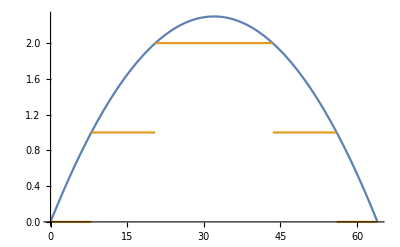

```mathematica
Block[{n=8},Plot[{7 2^(-3+n) -√(49 4^(-3+n)-2^(-2+n) i+i^2),FlipRegion[i,n]},{i,0,2^(n-2)}]]
```

So for a given i and a given n we can determine how many times the peaks have passed each other.

What happens when peaks pass? The intercepts are bound in some form matching ..

```mathematica
Clear[limitsX];
limitsX[i_,a_,b_,n_,oddIndxQ_,oddIotaQ_]=Module[{},
If[Xnor[oddIndxQ,oddIotaQ],
{{extremaB[b,n],extremaA[a,n]},interX[i,n],{extremaA[a+1,n],extremaB[b+1,n]}},
{{extremaA[a,n],extremaB[b,n]},interX[i,n],{extremaB[b+1,n],extremaA[a+1,n]}}
]
];
limitsX[i_,n_]=Module[{ι},
ι=FlipRegion[i,n];
limitsX[i,i+ι,i-1-ι,n,OddQ[i],OddQ[ι]]
];
```

Initially we have

```mathematica
Grid[{{TraditionalForm[crossDisplay[limitsX[i, i, i - 1, n, True,  False]]], " i ∈ {2ℕ+1}"}, 
      {TraditionalForm[crossDisplay[limitsX[i, i, i - 1, n, False, False]]], " i ∈ {2ℕ}"}}]
```

(ϕ^o)_a(i,n)
(ϕ^o)_b(i-1,n)  <  ϕ^x(i,n)  <  (ϕ^o)_b(i,n)
(ϕ^o)_a(i+1,n) |  i ∈ {2ℕ+1}
(ϕ^o)_b(i-1,n)
(ϕ^o)_a(i,n)  <  ϕ^x(i,n)  <  (ϕ^o)_a(i+1,n)
(ϕ^o)_b(i,n) |  i ∈ {2ℕ}

After a flip

```mathematica
Grid[{{TraditionalForm[crossDisplay[limitsX[i, i+ι,i-1-ι, n, True,  True]]], " i ∈ {2ℕ+1}"}, 
      {TraditionalForm[crossDisplay[limitsX[i, i+ι,i-1-ι, n, False, True]]], " i ∈ {2ℕ}"}}]/.ι->1
```

(ϕ^o)_b(i-2,n)
(ϕ^o)_a(i+1,n)  <  ϕ^x(i,n)  <  (ϕ^o)_a(i+2,n)
(ϕ^o)_b(i-1,n) |  i ∈ {2ℕ+1}
(ϕ^o)_a(i+1,n)
(ϕ^o)_b(i-2,n)  <  ϕ^x(i,n)  <  (ϕ^o)_b(i-1,n)
(ϕ^o)_a(i+2,n) |  i ∈ {2ℕ}

After ι flips

```mathematica
Column[{Row[{"ι = ",TraditionalForm[FlipRegion[i,n]]}],
Row[{TraditionalForm[crossDisplay[limitsX[i, i+ι,i-1-ι, n, True,  True]]],   "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )"}], 
      Row[{TraditionalForm[crossDisplay[limitsX[i, i+ι,i-1-ι, n, False, True]]], "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )"}]}]
```

ι = Floor[7 2^(n-3)-√(i^2-i 2^(n-2)+49 4^(n-3))]
(ϕ^o)_b(i-ι-1,n)
(ϕ^o)_a(i+ι,n)  <  ϕ^x(i,n)  <  (ϕ^o)_a(i+ι+1,n)
(ϕ^o)_b(i-ι,n)    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )
(ϕ^o)_a(i+ι,n)
(ϕ^o)_b(i-ι-1,n)  <  ϕ^x(i,n)  <  (ϕ^o)_b(i-ι,n)
(ϕ^o)_a(i+ι+1,n)    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )

We can now generalise to points where the extrema are not at 1

```mathematica
genInter=Together@Expand@{
intersectionFromPoints[{{extremaB[i-ι-1,n],β}, {extremaB[i-ι,n],0}}, {{extremaA[i+ι,n],0}, {extremaA[i+ι+1,n],α}}],
intersectionFromPoints[{{extremaA[i+ι,n],α }, {extremaA[i+ι+1,n],0}}, {{extremaB[i-ι-1,n],0}, {extremaB[i-ι,n],β}}]
};
genInter=MapAt[Collect[#,{α,β},Simplify]&,
genInter
,{{1,1,2},{1,1,1,1},{1,2,2},{1,2,1,1},{2,1,2},{2,1,1,1},{2,2,2,1},{2,2,1}}];
TraditionalForm[evenInter]
```

((α (ϕ^o)_a(i+ι) ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι))+β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1)) (ϕ^o)_b(i-ι))/(β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1))+α ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι))) | (α β ((ϕ^o)_a(i+ι)-(ϕ^o)_b(i-ι)))/(β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1))+α ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι)))
(β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1)) (ϕ^o)_b(i-ι-1)+α (ϕ^o)_a(i+ι+1) ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι)))/(β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1))+α ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι))) | (α β ((ϕ^o)_b(i-ι-1)-(ϕ^o)_a(i+ι+1)))/(β ((ϕ^o)_a(i+ι)-(ϕ^o)_a(i+ι+1))+α ((ϕ^o)_b(i-ι-1)-(ϕ^o)_b(i-ι))))

```mathematica
Column[{Row[{"ι = ",TraditionalForm[FlipRegion[i,n]]}],
Row[{"τ > ",TraditionalForm[genInterX[α,β,i,ι,n,True,True][[2]]],   "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )"}], 
      Row[{"τ > ",TraditionalForm[genInterX[α,β,i,ι,n,False,True][[2]]], "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )"}],
Row[{"θ = ",TraditionalForm[genInterX[α,β,i,ι,n,True,True][[1]]],   "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )"}], 
      Row[{"θ = ",TraditionalForm[genInterX[α,β,i,ι,n,False,True][[1]]], "    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )"}]}]
```

ι = Floor[7 2^(n-3)-√(i^2-i 2^(n-2)+49 4^(n-3))]
τ > (α β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_b(i-ι,n)))/(β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n))+α ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n)))    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )
τ > (α β ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_a(i+ι+1,n)))/(β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n))+α ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n)))    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )
θ = (α (ϕ^o)_a(i+ι,n) ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n))+β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n)) (ϕ^o)_b(i-ι,n))/(β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n))+α ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n)))    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ+1} ) ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ} )
θ = (α (ϕ^o)_a(i+ι+1,n) ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n))+β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n)) (ϕ^o)_b(i-ι-1,n))/(β ((ϕ^o)_a(i+ι,n)-(ϕ^o)_a(i+ι+1,n))+α ((ϕ^o)_b(i-ι-1,n)-(ϕ^o)_b(i-ι,n)))    ( i ∈ {2ℕ+1} ∧ ι ∈ {2ℕ} )   ∨  ( i ∈ {2ℕ} ∧ ι ∈ {2ℕ+1} )

```mathematica
{genInterX[α,β,i,ι,n,True,True][[2]] ,genInterX[α,β,i+1,ι,n,False,True][[2]]}/.thetaRules
```

{(α β (-ArcTan[(2^(2-n) (i-ι))/(√3)]+ArcTan[(√3 (i+ι))/(2^n-i-ι)]))/(α (ArcTan[(2^(2-n) (-1+i-ι))/(√3)]-ArcTan[(2^(2-n) (i-ι))/(√3)])+β (ArcTan[(√3 (i+ι))/(2^n-i-ι)]-ArcTan[(√3 (1+i+ι))/(-1+2^n-i-ι)])),(α β (ArcTan[(2^(2-n) (i-ι))/(√3)]-ArcTan[(√3 (2+i+ι))/(-2+2^n-i-ι)]))/(α (ArcTan[(2^(2-n) (i-ι))/(√3)]-ArcTan[(2^(2-n) (1+i-ι))/(√3)])+β (ArcTan[(√3 (1+i+ι))/(-1+2^n-i-ι)]-ArcTan[(√3 (2+i+ι))/(-2+2^n-i-ι)]))}

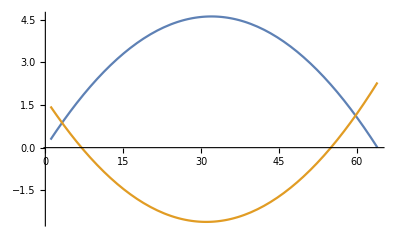
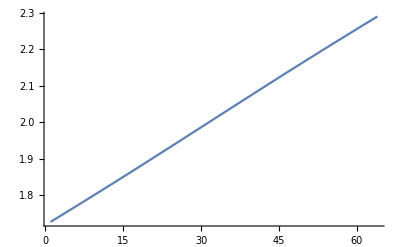
{(4 (-ArcTan[i/(64 √3)]+ArcTan[(√3 i)/(256-i)]))/(2 (ArcTan[(-1+i)/(64 √3)]-ArcTan[i/(64 √3)])+2 (ArcTan[(√3 i)/(256-i)]-ArcTan[(√3 (1+i))/(255-i)])),(4 (ArcTan[i/(64 √3)]-ArcTan[(√3 (2+i))/(254-i)]))/(2 (ArcTan[i/(64 √3)]-ArcTan[(1+i)/(64 √3)])+2 (ArcTan[(√3 (1+i))/(255-i)]-ArcTan[(√3 (2+i))/(254-i)]))}
-Graphics-
-Graphics-

```mathematica
Block[{n=8,α=2,β=2,ι=0},
f={genInterX[α,β,i,ι,n,True,True][[2]] ,genInterX[α,β,i+1,ι,n,False,True][[2]]}/.thetaRules;
Column[{
f,Plot[f,{i,1,2^(n-2)}],
Plot[f[[1]]+f[[2]],{i,1,2^(n-2)}]
}]
]
```

```mathematica
drawIntersection[ptsNew_,ptsNames_,opts:OptionsPattern[]]:=Module[{inter,ht1,ht2,heights1,heights2,base1,base2,a,b},
inter=intersectionFromPoints[{ ptsNew[[1,1]], ptsNew[[3,2]]},{ ptsNew[[1,2]], ptsNew[[3,1]]}];
a=  ptsNew[[3,1,1]]- ptsNew[[1,1,1]];
b= ptsNew[[3,2,1]]- ptsNew[[1,2,1]];
thetaRange={Min@@ptsNew[[1,All,1]],Max@@ptsNew[[3,All,1]]};
margin=0.2(thetaRange[[2]]-thetaRange[[1]]);
thetaRange={thetaRange[[1]]-margin,thetaRange[[2]]+margin};
ht1=inter[[2]];
ht2=(2-inter[[2]]);
hights1={Black,Dashed,Line[{{inter[[1]],0},inter}],Text[Style[h1,Medium,Bold],{inter[[1]],ht1/3},{0,0},{1,0},Background->None]};
hights2={Darker[Orange],Dashed,Line[{{inter[[1]],2},inter}],Text[Style[h2,Medium,Bold],{inter[[1]],2-ht2/2},{0,0},{1,0},Background->None]};
base1={Darker[Orange],Dashed,Line[{ ptsNew[[1,1]], ptsNew[[3,1]]}],Text[Style["a",Medium,Bold],{(  ptsNew[[3,1,1]]+ ptsNew[[1,1,1]])/2,2},{0,-1},{1,0},Background->None],
Text[Style[ptsNames[[1,1]],Medium,Bold,Black], ptsNew[[1,1]],{1,0},{1,0},Background->None],
Text[Style[ptsNames[[3,1]],Medium,Bold,Black], ptsNew[[3,1]],{-1,0},{1,0},Background->None]};
base2={Darker[Orange],Dashed,Line[{ ptsNew[[1,2]], ptsNew[[3,2]]}],Text[Style["b",Medium,Bold],( ptsNew[[1,2]]+ ptsNew[[3,2]])/2,{0,1},{1,0},Background->None],
Text[Style[ptsNames[[1,2]],Medium,Bold,Black], ptsNew[[1,2]],{1,0},{1,0},Background->None],
Text[Style[ptsNames[[3,2]],Medium,Bold,Black], ptsNew[[3,2]],{-1,0},{1,0},Background->None]};
interPoint={Black,Text[Style[ "  "<>ptsNames[[2]],Medium,Bold,Black], ptsNew[[2]],{-1,0},{1,0},Background->None]};
Graphics[{Line[{ ptsNew[[1,1]], ptsNew[[3,2]]}],Line[{ ptsNew[[1,2]], ptsNew[[3,1]]}],Green,DrawAngle[ ptsNew[[3,1]], ptsNew[[1,2]], ptsNew[[3,2]]],Blue,DrawAngle[ ptsNew[[1,1]], ptsNew[[3,2]], ptsNew[[1,2]]],Purple,DrawAngle[ ptsNew[[3,1]], ptsNew[[1,1]], ptsNew[[3,2]]],Yellow,DrawAngle[ ptsNew[[1,1]], ptsNew[[3,1]], ptsNew[[1,2]]],Orange,DrawAngle[ ptsNew[[1,1]],inter, ptsNew[[3,1]]],DrawAngle[ ptsNew[[1,2]],inter, ptsNew[[3,2]]],hights1,hights2,base1,base2,interPoint},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},PlotRange->{thetaRange,{-0.2,2.2}},AspectRatio->1,opts ]]
```

```mathematica
Clear[i,n,cond,thetaPts,pts,extremaAf,extremaBf,interXf]
Block[{n=8,pts},
crossDisplay[{{a_,b_},x_,{aa_,bb_}},valid_]:=Module[{col},
col={If[valid[[1]],Darker[Green],Darker[Red],Orange],If[valid[[2]],Darker[Green],Darker[Red],Orange]};
Row[{Column[{Style[a,col[[1]]],Style[b,col[[1]]]}],Row[{"  <  ",x,"  <  "}],Column[{Style[aa,col[[1]]],Style[bb,col[[1]]]}]}]
];
pntRules={
extremaA-> Function[{i,n},{thetaExtrema[i,n][[1]],If[OddQ[i],2,0]}],
extremaB-> Function[{i,n},{thetaExtrema[i,n][[2]],If[OddQ[i],2,0]}],
interX-> thetaIntersection};
thetaRules={
extremaA-> Function[{i,n},thetaExtrema[i,n][[1]]],
extremaB-> Function[{i,n},thetaExtrema[i,n][[2]]],
interX-> Function[{i,n},Evaluate[thetaIntersection[i,n][[1]]]]};
dispRules={
extremaA-> Function[{i,n},ToString[extremaA[i],TraditionalForm]],
extremaB-> Function[{i,n},ToString[extremaB[i],TraditionalForm]],
interX-> Function[{i,n},ToString[interX[i],TraditionalForm]]};
Column[Flatten[{
Table[ptsX=limitsX[i,n]/.pntRules;
thetaX=limitsX[i,n]/.thetaRules;
dispX=limitsX[i,n]/.dispRules;
valid={Less[thetaX[[1,1]],thetaX[[2]],thetaX[[3,1]]],Less[thetaX[[1,2]],thetaX[[2]],thetaX[[3,2]]]};
Labeled[drawIntersection[ptsX,dispX,ImageSize->250],Column[{Row[{"With"}],Row[{"n = ",n}],Row[{"i = ",i}],Row[{"ι = ",FlipRegion[i,n]}],crossDisplay[dispX,valid],crossDisplay[N[thetaX],valid]}],Right]
,{i,1,2^(n-2)-1,1}]
}]]
]
```

-Graphics-With
n = 8
i = 1
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.
0.00679225  <  0.00775195  <  0.0136373
0.00902085
-Graphics-With
n = 8
i = 2
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.00902085
0.0136373  <  0.0155425  <  0.0205353
0.0180402
-Graphics-With
n = 8
i = 3
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0180402
0.0205353  <  0.0233707  <  0.0274859
0.0270567
-Graphics-With
n = 8
i = 4
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0270567
0.0274859  <  0.0312357  <  0.0344893
0.0360687
-Graphics-With
n = 8
i = 5
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0360687
0.0344893  <  0.0391365  <  0.0415453
0.0450749
-Graphics-With
n = 8
i = 6
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0450749
0.0415453  <  0.0470721  <  0.0486538
0.0540738
-Graphics-With
n = 8
i = 7
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0540738
0.0486538  <  0.0550416  <  0.0558146
0.0630639
-Graphics-With
n = 8
i = 8
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0540738
0.0630276  <  0.0630438  <  0.0702926
0.0630639
-Graphics-With
n = 8
i = 9
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0630639
0.0702926  <  0.0710777  <  0.0776094
0.0720439
-Graphics-With
n = 8
i = 10
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0720439
0.0776094  <  0.0791423  <  0.0849777
0.0810122
-Graphics-With
n = 8
i = 11
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0810122
0.0849777  <  0.0872363  <  0.0923973
0.0899675
-Graphics-With
n = 8
i = 12
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0899675
0.0923973  <  0.0953587  <  0.0998679
0.0989083
-Graphics-With
n = 8
i = 13
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.0989083
0.0998679  <  0.103508  <  0.107389
0.107833
-Graphics-With
n = 8
i = 14
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.107833
0.107389  <  0.111684  <  0.114961
0.116741
-Graphics-With
n = 8
i = 15
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.116741
0.114961  <  0.119884  <  0.122583
0.12563
-Graphics-With
n = 8
i = 16
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.12563
0.122583  <  0.128108  <  0.130254
0.1345
-Graphics-With
n = 8
i = 17
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.1345
0.130254  <  0.136354  <  0.137974
0.143348
-Graphics-With
n = 8
i = 18
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.143348
0.137974  <  0.144621  <  0.145743
0.152173
-Graphics-With
n = 8
i = 19
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.152173
0.145743  <  0.152907  <  0.15356
0.160975
-Graphics-With
n = 8
i = 20
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.160975
0.15356  <  0.161212  <  0.161425
0.169751
-Graphics-With
n = 8
i = 21
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.160975
0.169338  <  0.169534  <  0.177296
0.169751
-Graphics-With
n = 8
i = 22
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.169751
0.177296  <  0.177872  <  0.185301
0.178502
-Graphics-With
n = 8
i = 23
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.178502
0.185301  <  0.186224  <  0.193351
0.187224
-Graphics-With
n = 8
i = 24
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.187224
0.193351  <  0.194588  <  0.201446
0.195918
-Graphics-With
n = 8
i = 25
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.195918
0.201446  <  0.202964  <  0.209584
0.204582
-Graphics-With
n = 8
i = 26
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.204582
0.209584  <  0.211351  <  0.217766
0.213216
-Graphics-With
n = 8
i = 27
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.213216
0.217766  <  0.219746  <  0.225991
0.221816
-Graphics-With
n = 8
i = 28
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.221816
0.225991  <  0.228148  <  0.234257
0.230384
-Graphics-With
n = 8
i = 29
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.230384
0.234257  <  0.236556  <  0.242564
0.238917
-Graphics-With
n = 8
i = 30
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.238917
0.242564  <  0.244968  <  0.250911
0.247416
-Graphics-With
n = 8
i = 31
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.247416
0.250911  <  0.253383  <  0.259297
0.255877
-Graphics-With
n = 8
i = 32
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.255877
0.259297  <  0.261799  <  0.267722
0.264302
-Graphics-With
n = 8
i = 33
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.264302
0.267722  <  0.270216  <  0.276183
0.272688
-Graphics-With
n = 8
i = 34
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.272688
0.276183  <  0.278631  <  0.284681
0.281035
-Graphics-With
n = 8
i = 35
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.281035
0.284681  <  0.287043  <  0.293215
0.289342
-Graphics-With
n = 8
i = 36
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.289342
0.293215  <  0.295451  <  0.301782
0.297608
-Graphics-With
n = 8
i = 37
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.297608
0.301782  <  0.303853  <  0.310383
0.305832
-Graphics-With
n = 8
i = 38
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.305832
0.310383  <  0.312248  <  0.319016
0.314014
-Graphics-With
n = 8
i = 39
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.314014
0.319016  <  0.320634  <  0.32768
0.322153
-Graphics-With
n = 8
i = 40
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.322153
0.32768  <  0.32901  <  0.336374
0.330248
-Graphics-With
n = 8
i = 41
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.330248
0.336374  <  0.337375  <  0.345097
0.338298
-Graphics-With
n = 8
i = 42
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.338298
0.345097  <  0.345727  <  0.353847
0.346302
-Graphics-With
n = 8
i = 43
ι = 2
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.346302
0.353847  <  0.354065  <  0.362624
0.354261
-Graphics-With
n = 8
i = 44
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.362173
0.353847  <  0.362386  <  0.362624
0.370038
-Graphics-With
n = 8
i = 45
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.370038
0.362624  <  0.370691  <  0.371426
0.377856
-Graphics-With
n = 8
i = 46
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.377856
0.371426  <  0.378978  <  0.380251
0.385625
-Graphics-With
n = 8
i = 47
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.385625
0.380251  <  0.387245  <  0.389099
0.393345
-Graphics-With
n = 8
i = 48
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.393345
0.389099  <  0.395491  <  0.397969
0.401016
-Graphics-With
n = 8
i = 49
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.401016
0.397969  <  0.403715  <  0.406858
0.408638
-Graphics-With
n = 8
i = 50
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.408638
0.406858  <  0.411915  <  0.415766
0.41621
-Graphics-With
n = 8
i = 51
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.41621
0.415766  <  0.420091  <  0.424691
0.423731
-Graphics-With
n = 8
i = 52
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.423731
0.424691  <  0.42824  <  0.433631
0.431201
-Graphics-With
n = 8
i = 53
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.431201
0.433631  <  0.436362  <  0.442587
0.438621
-Graphics-With
n = 8
i = 54
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.438621
0.442587  <  0.444457  <  0.451555
0.445989
-Graphics-With
n = 8
i = 55
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.445989
0.451555  <  0.452521  <  0.460535
0.453306
-Graphics-With
n = 8
i = 56
ι = 1
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.453306
0.460535  <  0.460555  <  0.469525
0.460571
-Graphics-With
n = 8
i = 57
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.467784
0.460535  <  0.468557  <  0.469525
0.474945
-Graphics-With
n = 8
i = 58
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.474945
0.469525  <  0.476527  <  0.478524
0.482053
-Graphics-With
n = 8
i = 59
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.482053
0.478524  <  0.484462  <  0.48753
0.489109
-Graphics-With
n = 8
i = 60
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.489109
0.48753  <  0.492363  <  0.496542
0.496113
-Graphics-With
n = 8
i = 61
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.496113
0.496542  <  0.500228  <  0.505559
0.503064
-Graphics-With
n = 8
i = 62
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.503064
0.505559  <  0.508056  <  0.514578
0.509961
-Graphics-With
n = 8
i = 63
ι = 0
TraditionalForm`
TraditionalForm`  <  TraditionalForm`  <  TraditionalForm`
TraditionalForm`
0.509961
0.514578  <  0.515847  <  0.523599
0.516807

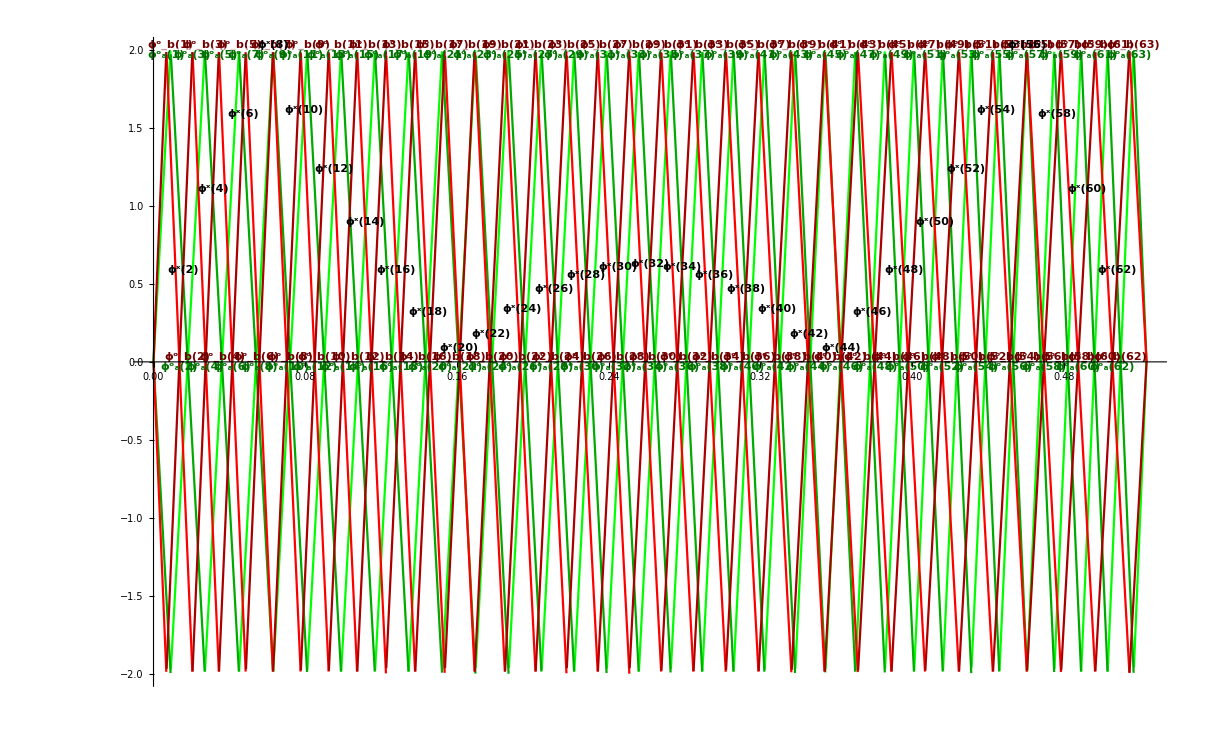

```mathematica
Block[{minAf,minBf,maxAf,maxBf,n=8,pts},
extremaAf=Function[{i},Evaluate[thetaExtrema[i,n][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,n][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,n][[1]]]];
maxBs=Table[
Text[Style[TraditionalForm[extremaB[i]],Medium,Bold,Darker@Darker@Red],{extremaBf[i],2},{0,-1},{1,0},Background->None]
,{i,1,2^(n-2)-1,2}];
minBs=Table[
Text[Style[TraditionalForm[extremaB[i]],Medium,Bold,Darker@Darker@Red],{extremaBf[i],0},{0,-1},{1,0},Background->None]
,{i,2,2^(n-2)-1,2}];
maxAs=Table[pt={extremaAf[i],2};{
White,Opacity[0.6],Disk[pt,0.01],Opacity[1],
Text[Style[TraditionalForm[extremaA[i]],Medium,Bold,Darker@Darker@Green],pt,{0,1},{1,0},Background->None]
}
,{i,1,2^(n-2)-1,2}];
minAs=Table[
Text[Style[TraditionalForm[extremaA[i]],Medium,Bold,Darker@Darker@Green],{extremaAf[i],0},{0,1},{1,0},Background->None]
,{i,2,2^(n-2)-1,2}];
interXs=Table[
Text[Style[TraditionalForm[interX[i]],Medium,Bold,Black],thetaIntersection[i,n],{0,-1},{1,0},Background->None]
,{i,2,2^(n-2)-1,2}];
plotRegionsFromList[t_,color_:Blue,opacity_:0.6,text_:Null,yRange_:{0,2},opts:OptionsPattern[]];
Plot[Evaluate[Flatten[distinctErrorFunc[θ,n,Round]]],{θ,0,Pi/6},PlotStyle->{Green,Darker[Green],Red,Darker[Red]}, Epilog->Flatten[{maxBs,minBs,maxAs,minAs,interXs}]]

]
```

## The Extrema Order between channels.

```mathematica
Clear[minAf,minBf,maxAf,maxBf,m,n];Block[{minAf,minBf,maxAf,maxBf,m,n,cond,solRule}, (* These functions are inide the ArcTan *)
minAf=Function[{m,n},thetaMin[m,n][[1,1]]];
minBf=Function[{m,n},thetaMin[m,n][[2,1]]];
maxAf=Function[{m,n},thetaMax[m,n][[1,1]]];
maxBf=Function[{m,n},thetaMax[m,n][[2,1]]];
cond={minBf[m,n]==minAf[m+1,n],maxBf[m,n]==maxAf[m+1,n]};
Print["The conditions are ",cond];
solRule=Map[approxSimplify[Reduce[#]]&,cond];
MatrixForm[approxSimplify[m/.Map[Solve[#,m]&,solRule]]]
]
```

The conditions are {(2^(3-n) m)/(√3)==(2 √3 (1+m))/(2^n-2 (1+m)),(2^(2-n) (1+2 m))/(√3)==(√3 (1+2 (1+m)))/(-1+2^n-2 (1+m))}

(1/16 (-8+2^n-√(64-7 2^(4+n)+4^n)) | 1/16 (-8+2^n+√(64-7 2^(4+n)+4^n))
1/16 (-16+2^n-√(64-7 2^(4+n)+4^n)) | 1/16 (-16+2^n+√(64-7 2^(4+n)+4^n)))

Possible forms

```mathematica
Reduce[1/16 √(64+2^(2 n)-7 2^(4+n))== 1/2 √(1-14 2^(n-3)+ 2^(2(n-3)))== 1/2 √((2^(n-3)-7)^2-48)]
```

True

There are flips when 2^(n-3) >= 14 ie n >= 7

```mathematica
ThetaFlipE=Function[{n},1/2 √((2^(n-3)-7)^2-48)];
ThetaFlip=Function[{n},{{ ((2^(n-3)-1)/2)-ThetaFlipE[n], ((2^(n-3)-1)/2)+ThetaFlipE[n]},{((2^(n-3)-1)/2)-1/2- ThetaFlipE[n],((2^(n-3)-1)/2)-1/2+ ThetaFlipE[n]}}];
ThetaCondL=Function[{m,n},If[n≥ 7,((2^(n-3)-1)/2)-ThetaFlipE[n]≤ m≤ ((2^(n-3)-1)/2)+ThetaFlipE[n],False]];
ThetaOpL=Function[{m,n},If[ThetaCondL[m,n],Greater,Less]]
```

Function[{m,n},If[ThetaCondL[m,n],Greater,Less]]

```mathematica
Block[{minAf,minBf,maxAf,maxBf,n=8},
Function[{m},Evaluate[thetaMin[m,n][[1]]]]
]
```

```mathematica
inter
```

```mathematica
extremaAf=Function[{i},Evaluate[thetaExtrema[i,8][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,8][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,8]]];
pts=Function[{i},
If[EvenQ[i],
{{{extremaB[i-1],1},{extremaA[i+1],1}},
{{extremaA[i],0},{extremaB[i],0}}},
{{{extremaA[i],1},{extremaB[i],1}},
{{extremaB[i-1],0},{extremaA[i+1],0}}}
]];
i=7
drawIntersection[pts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf},Map[ToString[#,TraditionalForm]&,pts[i][[All,All,1]],{2}]]
```

7

```mathematica
pts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}
```

{{{ArcTan[(√3 i)/(256-i)],1},{ArcTan[i/(64 √3)],1}},{{ArcTan[(-1+i)/(64 √3)],0},{ArcTan[(√3 (1+i))/(255-i)],0}}}

```mathematica
N@thetaIntersection[1,8]
```

{0.00775195,1.71866}

```mathematica
cond=Function[{i},
If[ThetaOpL[(i-1)/2,n][1,2],
If[EvenQ[i],
{{Less[extremaB[i-1],interX[i],extremaA[i+1]]},
{extremaA[i]<interX[i]<extremaB[i]}},
{{extremaA[i]<interX[i]<extremaB[i]},
{Less[extremaB[i-1],interX[i],extremaA[i+1]]}}
],
If[EvenQ[i],
{{Less[extremaA[i+1],interX[i],extremaB[i-1]]},
{extremaA[i+2]<interX[i]<extremaB[i-2]}},
{{extremaA[i]<interX[i]<extremaB[i]},
{Less[extremaB[i-1],interX[i],extremaA[i+1]]}}
]
]
];
```

```mathematica
ThetaCondL[(15-1)/2,8]
```

True

```mathematica
drawIntersection[pts_,ptsNames_,interIn_,interInName_]:=Module[{inter,ht1,ht2,heights1,heights2,base1,base2,a,b},
inter=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
a=pts[[1,2,1]]-pts[[1,1,1]];
b=pts[[2,2,1]]-pts[[2,1,1]];
ht1=inter[[2]];
ht2=(1-inter[[2]]);
hights1={Black,Dashed,Line[{{(pts[[1,2,1]]+pts[[1,1,1]])/2,0},inter}],Text[Style[h1,Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,ht1/3},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{(pts[[1,2,1]]+pts[[1,1,1]])/2,1},inter}],Text[Style[h2,Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,1-ht2/2},{0,0},{1,0},Background->White]};
base1={Darker[Orange],Dashed,Line[{pts[[1,1]],pts[[1,2]]}],Text[Style["a",Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,1},{0,-1},{1,0},Background->White],
Text[Style[ptsNames[[1,1]],Medium,Bold,Black],pts[[1,1]],{0,-1},{1,0},Background->White],
Text[Style[ptsNames[[1,2]],Medium,Bold,Black],pts[[1,2]],{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,2]]}],Text[Style["b",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White],
Text[Style[ptsNames[[2,1]],Medium,Bold,Black],pts[[2,1]],{0,1},{1,0},Background->White],
Text[Style[ptsNames[[2,2]],Medium,Bold,Black],pts[[2,2]],{0,1},{1,0},Background->White]};
interPoint={Black,Text[Style[interInName,Medium,Bold,Black],interIn,{0,-1},{1,0},Background->White]};
Graphics[{Line[{pts[[1,1]],pts[[2,2]]}],Line[{pts[[2,1]],pts[[1,2]]}],Green,DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],Blue,DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],Purple,DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],Yellow,DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],Orange,DrawAngle[pts[[1,1]],inter,pts[[1,2]]],DrawAngle[pts[[2,1]],inter,pts[[2,2]]],hights1,hights2,base1,base2,interPoint},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},PlotRange->{{0.9 Min[pts[[1,1,1]],pts[[2,1,1]]],1.1Max[pts[[1,2,1]],pts[[2,2,1]]]},{-0.2,2.2}},AspectRatio->1 ]]
```

```mathematica
Flatten[distinctErrorFunc[θ,8,Round]]
```

{-4 Round[32 √3 Tan[Mod[θ,π/6]]]+128 √3 Tan[Mod[θ,π/6]],4 Round[32 √3 Tan[Mod[θ,π/6]]]-128 √3 Tan[Mod[θ,π/6]],4 Round[64 Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]-256 Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]],-4 Round[64 Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+256 Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}

```mathematica
crossDisplay[{{a_,b_},x_,{aa_,bb_}}]:=Row[{Column[{a,b}],x,Column[{aa,bb}]}];
```

```mathematica
n
```

n

```mathematica
Block[{n=8,i=20},Column[{cond[i],TraditionalForm[crossDisplay[thetaPts[i]]],crossDisplay[thetaPts[i]],FullForm[thetaPts[i]],thetaPts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf},N[thetaPts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}],N[TraditionalForm[crossDisplay[thetaPts[i]]]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}]}]]
```

{{extremaA[21]<interX[20]<extremaB[19]},{extremaB[18]<interX[20]<extremaA[22]}}
(ϕ^o)_a(21)
(ϕ^o)_b(18)ϕ^x(20)(ϕ^o)_b(19)
(ϕ^o)_a(22)
extremaA[21]
extremaB[18]interX[20]extremaB[19]
extremaA[22]
List[List[extremaA[21],extremaB[18]],interX[20],List[extremaB[19],extremaA[22]]]
{{ArcTan[(21 √3)/235],ArcTan[(3 √3)/32]},ArcTan[(-51/8+(√3081)/8)/(2 √3)],{ArcTan[19/(64 √3)],ArcTan[11/(39 √3)]}}
{{0.15356,0.160975},0.161212,{0.169751,0.161425}}
0.15356
0.1609750.1612120.169751
0.161425

```mathematica
List[List[extremaA[21],extremaB[18]],interX[20],List[extremaB[19],extremaA[22]]]/.{extremaA->N@extremaAf,extremaB->N@extremaBf,interX->N@interXf}
```

{{0.15356,0.160975},0.161212,{0.169751,0.161425}}

```mathematica
N@List[List[extremaAf[21],extremaBf[18]],interXf[20],List[extremaBf[19],extremaAf[22]]]
```

{{0.15356,0.160975},0.161212,{0.169751,0.161425}}

```mathematica
extremaAf[22]
```

ArcTan[11/(39 √3)]

```mathematica
N@extremaAf[22]
```

0.161425

```mathematica
N@{{extremaAf[21],"<",interXf[20],"<",extremaBf[19]},{extremaBf[18],"<",interXf[20],"<",extremaAf[22]}}
```

{{0.15356,<,0.161212,<,0.169751},{0.160975,<,0.161212,<,0.161425}}

```mathematica
{{0.15291992347341635}, {0.16097475883750662}}0.16121228514772518{{0.16975135467516367}, {0.16008079736851585}}
```

```mathematica
Clear[minAf,minBf,maxAf,maxBf,i,n]
Block[{minAf,minBf,maxAf,maxBf,n=8,pts},
extremaAf=Function[{i},Evaluate[thetaExtrema[i,n][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,n][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,n][[1]]]];
thetaPts=Function[{i},
If[ThetaCondL[(i-1)/2,n],s=2,s=0];
If[ThetaCondL[(i-1)/2,n],
If[EvenQ[i],
{{extremaA[1+i],extremaB[i-s]},interX[i],{extremaB[-1+i],extremaA[i+s]}},
{{extremaB[i-s],extremaA[1+i]},interX[i],{extremaA[i+s],extremaB[-1+i]}}
],
If[EvenQ[i],
{{extremaB[-1+i],extremaA[i+s]},interX[i],{extremaA[1+i],extremaB[i-s]}},
{{extremaA[i+s],extremaB[-1+i]},interX[i],{extremaB[i-s],extremaA[1+i]}}
]
]
];
cond=Function[{i},
If[ThetaCondL[(i-1)/2,n],s=2,s=0];
If[EvenQ[i],
{{ThetaOpL[(i-1)/2,n][extremaB[i-1],interX[i],extremaA[i+1]]},
{ThetaOpL[(i-1)/2,n][extremaA[i+s],interX[i],extremaB[i-s]]}},
{{ThetaOpL[(i-1)/2,n][extremaA[i+s],interX[i],extremaB[i-s]]},
{ThetaOpL[(i-1)/2,n][extremaB[i-1],interX[i],extremaA[i+1]]}}
]
];
pts=Function[{i},
If[ThetaCondL[(i-1)/2,n],s=2,s=0];
If[ThetaCondL[(i-1)/2,n],
If[EvenQ[i],
{{{extremaA[i+1],2},{extremaB[i-1],2}},
{{extremaB[i-s],0},{extremaA[i+s],0}}},
{{{extremaB[i-s],2},{extremaA[i+s],2}},
{{extremaA[i+1],0},{extremaB[i-1],0}}}
],
If[EvenQ[i],
{{{extremaB[i-1],2},{extremaA[i+1],2}},
{{extremaA[i+s],0},{extremaB[i-s],0}}},
{{{extremaA[i+s],2},{extremaB[i-s],2}},
{{extremaB[i-1],0},{extremaA[i+1],0}}}
]
]
];
Column[Flatten[{
Table[Row[{i,
TraditionalForm[cond[i]]," = ",
MatrixForm[cond[i]]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}," = ",TraditionalForm[pts[i][[All,All,1]]]," = ",
TraditionalForm[crossDisplay[thetaPts[i]]],
TraditionalForm[crossDisplay[thetaPts[i]]]/.{extremaA->N@extremaAf,extremaB->N@extremaBf,interX->N@interXf}," = ",
MatrixForm[cond[i]]/.{Less[a_,b_]:>Row[{a,"<",b}],Greater[a_,b_]:>Row[{a,">",b}]}/.{extremaA->N@extremaAf,extremaB->N@extremaBf,interX->N@interXf},
drawIntersection[pts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf},Map[ToString[#,TraditionalForm]&,pts[i][[All,All,1]],{2}],thetaIntersection[i,n],TraditionalForm[interX[i]]]}]
,{i,1,2^(n-2)-1,1}]
}]]]
```

1((ϕ^o)_a(1)<ϕ^x(1)<(ϕ^o)_b(1)
(ϕ^o)_b(0)<ϕ^x(1)<(ϕ^o)_a(2)) = (True
True) = ((ϕ^o)_a(1) | (ϕ^o)_b(1)
(ϕ^o)_b(0) | (ϕ^o)_a(2)) = (ϕ^o)_a(1)
(ϕ^o)_b(0)ϕ^x(1)(ϕ^o)_b(1)
(ϕ^o)_a(2)0.00679225
0.0.007751950.00902085
0.0135839 = (True
True)-Graphics-
2((ϕ^o)_b(1)<ϕ^x(2)<(ϕ^o)_a(3)
(ϕ^o)_a(2)<ϕ^x(2)<(ϕ^o)_b(2)) = (True
True) = ((ϕ^o)_b(1) | (ϕ^o)_a(3)
(ϕ^o)_a(2) | (ϕ^o)_b(2)) = (ϕ^o)_b(1)
(ϕ^o)_a(2)ϕ^x(2)(ϕ^o)_a(3)
(ϕ^o)_b(2)0.00902085
0.01363730.01554250.0204544
0.0180402 = (True
True)-Graphics-
3((ϕ^o)_a(3)<ϕ^x(3)<(ϕ^o)_b(3)
(ϕ^o)_b(2)<ϕ^x(3)<(ϕ^o)_a(4)) = (True
True) = ((ϕ^o)_a(3) | (ϕ^o)_b(3)
(ϕ^o)_b(2) | (ϕ^o)_a(4)) = (ϕ^o)_a(3)
(ϕ^o)_b(2)ϕ^x(3)(ϕ^o)_b(3)
(ϕ^o)_a(4)0.0205353
0.01804020.02337070.0270567
0.0273774 = (True
True)-Graphics-
4((ϕ^o)_b(3)<ϕ^x(4)<(ϕ^o)_a(5)
(ϕ^o)_a(4)<ϕ^x(4)<(ϕ^o)_b(4)) = (True
True) = ((ϕ^o)_b(3) | (ϕ^o)_a(5)
(ϕ^o)_a(4) | (ϕ^o)_b(4)) = (ϕ^o)_b(3)
(ϕ^o)_a(4)ϕ^x(4)(ϕ^o)_a(5)
(ϕ^o)_b(4)0.0270567
0.02748590.03123570.0343526
0.0360687 = (True
True)-Graphics-
5((ϕ^o)_a(5)<ϕ^x(5)<(ϕ^o)_b(5)
(ϕ^o)_b(4)<ϕ^x(5)<(ϕ^o)_a(6)) = (True
True) = ((ϕ^o)_a(5) | (ϕ^o)_b(5)
(ϕ^o)_b(4) | (ϕ^o)_a(6)) = (ϕ^o)_a(5)
(ϕ^o)_b(4)ϕ^x(5)(ϕ^o)_b(5)
(ϕ^o)_a(6)0.0344893
0.03606870.03913650.0450749
0.04138 = (True
True)-Graphics-
6((ϕ^o)_b(5)<ϕ^x(6)<(ϕ^o)_a(7)
(ϕ^o)_a(6)<ϕ^x(6)<(ϕ^o)_b(6)) = (True
True) = ((ϕ^o)_b(5) | (ϕ^o)_a(7)
(ϕ^o)_a(6) | (ϕ^o)_b(6)) = (ϕ^o)_b(5)
(ϕ^o)_a(6)ϕ^x(6)(ϕ^o)_a(7)
(ϕ^o)_b(6)0.0450749
0.04154530.04707210.0484595
0.0540738 = (True
True)-Graphics-
7((ϕ^o)_a(7)<ϕ^x(7)<(ϕ^o)_b(7)
(ϕ^o)_b(6)<ϕ^x(7)<(ϕ^o)_a(8)) = (True
True) = ((ϕ^o)_a(7) | (ϕ^o)_b(7)
(ϕ^o)_b(6) | (ϕ^o)_a(8)) = (ϕ^o)_a(7)
(ϕ^o)_b(6)ϕ^x(7)(ϕ^o)_b(7)
(ϕ^o)_a(8)0.0486538
0.05407380.05504160.0630639
0.0555909 = (True
True)-Graphics-
8((ϕ^o)_b(7)>ϕ^x(8)>(ϕ^o)_a(9)
(ϕ^o)_a(10)>ϕ^x(8)>(ϕ^o)_b(6)) = (True
True) = ((ϕ^o)_a(9) | (ϕ^o)_b(7)
(ϕ^o)_b(6) | (ϕ^o)_a(10)) = (ϕ^o)_a(9)
(ϕ^o)_b(6)ϕ^x(8)(ϕ^o)_b(7)
(ϕ^o)_a(10)0.0627741
0.05407380.06304380.0630639
0.0697275 = (True
True)-Graphics-
9((ϕ^o)_a(11)>ϕ^x(9)>(ϕ^o)_b(7)
(ϕ^o)_b(8)>ϕ^x(9)>(ϕ^o)_a(10)) = (True
True) = ((ϕ^o)_b(7) | (ϕ^o)_a(11)
(ϕ^o)_a(10) | (ϕ^o)_b(8)) = (ϕ^o)_b(7)
(ϕ^o)_a(10)ϕ^x(9)(ϕ^o)_a(11)
(ϕ^o)_b(8)0.0630639
0.07000890.07107770.0769834
0.0720439 = (True
True)-Graphics-
10((ϕ^o)_b(9)>ϕ^x(10)>(ϕ^o)_a(11)
(ϕ^o)_a(12)>ϕ^x(10)>(ϕ^o)_b(8)) = (True
True) = ((ϕ^o)_a(11) | (ϕ^o)_b(9)
(ϕ^o)_b(8) | (ϕ^o)_a(12)) = (ϕ^o)_a(11)
(ϕ^o)_b(8)ϕ^x(10)(ϕ^o)_b(9)
(ϕ^o)_a(12)0.0772951
0.07204390.07914230.0810122
0.0842901 = (True
True)-Graphics-
11((ϕ^o)_a(13)>ϕ^x(11)>(ϕ^o)_b(9)
(ϕ^o)_b(10)>ϕ^x(11)>(ϕ^o)_a(12)) = (True
True) = ((ϕ^o)_b(9) | (ϕ^o)_a(13)
(ϕ^o)_a(12) | (ϕ^o)_b(10)) = (ϕ^o)_b(9)
(ϕ^o)_a(12)ϕ^x(11)(ϕ^o)_a(13)
(ϕ^o)_b(10)0.0810122
0.08463250.08723630.0916473
0.0899675 = (True
True)-Graphics-
12((ϕ^o)_b(11)>ϕ^x(12)>(ϕ^o)_a(13)
(ϕ^o)_a(14)>ϕ^x(12)>(ϕ^o)_b(10)) = (True
True) = ((ϕ^o)_a(13) | (ϕ^o)_b(11)
(ϕ^o)_b(10) | (ϕ^o)_a(14)) = (ϕ^o)_a(13)
(ϕ^o)_b(10)ϕ^x(12)(ϕ^o)_b(11)
(ϕ^o)_a(14)0.0920208
0.08996750.09535870.0989083
0.0990547 = (True
True)-Graphics-
13((ϕ^o)_a(15)>ϕ^x(13)>(ϕ^o)_b(11)
(ϕ^o)_b(12)>ϕ^x(13)>(ϕ^o)_a(14)) = (True
True) = ((ϕ^o)_b(11) | (ϕ^o)_a(15)
(ϕ^o)_a(14) | (ϕ^o)_b(12)) = (ϕ^o)_b(11)
(ϕ^o)_a(14)ϕ^x(13)(ϕ^o)_a(15)
(ϕ^o)_b(12)0.0989083
0.09945970.1035080.106512
0.107833 = (True
True)-Graphics-
14((ϕ^o)_b(13)>ϕ^x(14)>(ϕ^o)_a(15)
(ϕ^o)_a(16)>ϕ^x(14)>(ϕ^o)_b(12)) = (True
True) = ((ϕ^o)_a(15) | (ϕ^o)_b(13)
(ϕ^o)_b(12) | (ϕ^o)_a(16)) = (ϕ^o)_a(15)
(ϕ^o)_b(12)ϕ^x(14)(ϕ^o)_b(13)
(ϕ^o)_a(16)0.106949
0.1078330.1116840.116741
0.114019 = (True
True)-Graphics-
15((ϕ^o)_a(17)>ϕ^x(15)>(ϕ^o)_b(13)
(ϕ^o)_b(14)>ϕ^x(15)>(ϕ^o)_a(16)) = (True
True) = ((ϕ^o)_b(13) | (ϕ^o)_a(17)
(ϕ^o)_a(16) | (ϕ^o)_b(14)) = (ϕ^o)_b(13)
(ϕ^o)_a(16)ϕ^x(15)(ϕ^o)_a(17)
(ϕ^o)_b(14)0.116741
0.1144880.1198840.121575
0.12563 = (True
True)-Graphics-
16((ϕ^o)_b(15)>ϕ^x(16)>(ϕ^o)_a(17)
(ϕ^o)_a(18)>ϕ^x(16)>(ϕ^o)_b(14)) = (True
True) = ((ϕ^o)_a(17) | (ϕ^o)_b(15)
(ϕ^o)_b(14) | (ϕ^o)_a(18)) = (ϕ^o)_a(17)
(ϕ^o)_b(14)ϕ^x(16)(ϕ^o)_b(15)
(ϕ^o)_a(18)0.122077
0.125630.1281080.1345
0.12918 = (True
True)-Graphics-
17((ϕ^o)_a(19)>ϕ^x(17)>(ϕ^o)_b(15)
(ϕ^o)_b(16)>ϕ^x(17)>(ϕ^o)_a(18)) = (True
True) = ((ϕ^o)_b(15) | (ϕ^o)_a(19)
(ϕ^o)_a(18) | (ϕ^o)_b(16)) = (ϕ^o)_b(15)
(ϕ^o)_a(18)ϕ^x(17)(ϕ^o)_a(19)
(ϕ^o)_b(16)0.1345
0.1297150.1363540.136834
0.143348 = (True
True)-Graphics-
18((ϕ^o)_b(17)>ϕ^x(18)>(ϕ^o)_a(19)
(ϕ^o)_a(20)>ϕ^x(18)>(ϕ^o)_b(16)) = (True
True) = ((ϕ^o)_a(19) | (ϕ^o)_b(17)
(ϕ^o)_b(16) | (ϕ^o)_a(20)) = (ϕ^o)_a(19)
(ϕ^o)_b(16)ϕ^x(18)(ϕ^o)_b(17)
(ϕ^o)_a(20)0.137402
0.1433480.1446210.152173
0.144536 = (True
False)-Graphics-
19((ϕ^o)_a(21)>ϕ^x(19)>(ϕ^o)_b(17)
(ϕ^o)_b(18)>ϕ^x(19)>(ϕ^o)_a(20)) = (True
True) = ((ϕ^o)_b(17) | (ϕ^o)_a(21)
(ϕ^o)_a(20) | (ϕ^o)_b(18)) = (ϕ^o)_b(17)
(ϕ^o)_a(20)ϕ^x(19)(ϕ^o)_a(21)
(ϕ^o)_b(18)0.152173
0.1451370.1529070.152285
0.160975 = (False
True)-Graphics-
20((ϕ^o)_b(19)>ϕ^x(20)>(ϕ^o)_a(21)
(ϕ^o)_a(22)>ϕ^x(20)>(ϕ^o)_b(18)) = (True
True) = ((ϕ^o)_a(21) | (ϕ^o)_b(19)
(ϕ^o)_b(18) | (ϕ^o)_a(22)) = (ϕ^o)_a(21)
(ϕ^o)_b(18)ϕ^x(20)(ϕ^o)_b(19)
(ϕ^o)_a(22)0.15292
0.1609750.1612120.169751
0.160081 = (True
False)-Graphics-
21((ϕ^o)_a(23)>ϕ^x(21)>(ϕ^o)_b(19)
(ϕ^o)_b(20)>ϕ^x(21)>(ϕ^o)_a(22)) = (False
True) = ((ϕ^o)_b(19) | (ϕ^o)_a(23)
(ϕ^o)_a(22) | (ϕ^o)_b(20)) = (ϕ^o)_b(19)
(ϕ^o)_a(22)ϕ^x(21)(ϕ^o)_a(23)
(ϕ^o)_b(20)0.169751
0.160750.1695340.167923
0.178502 = (False
True)-Graphics-
22((ϕ^o)_b(21)>ϕ^x(22)>(ϕ^o)_a(23)
(ϕ^o)_a(24)>ϕ^x(22)>(ϕ^o)_b(20)) = (True
False) = ((ϕ^o)_a(23) | (ϕ^o)_b(21)
(ϕ^o)_b(20) | (ϕ^o)_a(24)) = (ϕ^o)_a(23)
(ϕ^o)_b(20)ϕ^x(22)(ϕ^o)_b(21)
(ϕ^o)_a(24)0.168628
0.1785020.1778720.187224
0.175812 = (True
False)-Graphics-
23((ϕ^o)_a(25)>ϕ^x(23)>(ϕ^o)_b(21)
(ϕ^o)_b(22)>ϕ^x(23)>(ϕ^o)_a(24)) = (False
True) = ((ϕ^o)_b(21) | (ϕ^o)_a(25)
(ϕ^o)_a(24) | (ϕ^o)_b(22)) = (ϕ^o)_b(21)
(ϕ^o)_a(24)ϕ^x(23)(ϕ^o)_a(25)
(ϕ^o)_b(22)0.187224
0.1765510.1862240.183746
0.195918 = (False
True)-Graphics-
24((ϕ^o)_b(23)>ϕ^x(24)>(ϕ^o)_a(25)
(ϕ^o)_a(26)>ϕ^x(24)>(ϕ^o)_b(22)) = (True
False) = ((ϕ^o)_a(25) | (ϕ^o)_b(23)
(ϕ^o)_b(22) | (ϕ^o)_a(26)) = (ϕ^o)_a(25)
(ϕ^o)_b(22)ϕ^x(24)(ϕ^o)_b(23)
(ϕ^o)_a(26)0.18452
0.1959180.1945880.204582
0.191725 = (True
False)-Graphics-
25((ϕ^o)_a(27)>ϕ^x(25)>(ϕ^o)_b(23)
(ϕ^o)_b(24)>ϕ^x(25)>(ϕ^o)_a(26)) = (False
True) = ((ϕ^o)_b(23) | (ϕ^o)_a(27)
(ϕ^o)_a(26) | (ϕ^o)_b(24)) = (ϕ^o)_b(23)
(ϕ^o)_a(26)ϕ^x(25)(ϕ^o)_a(27)
(ϕ^o)_b(24)0.204582
0.1925350.2029640.199748
0.213216 = (False
True)-Graphics-
26((ϕ^o)_b(25)>ϕ^x(26)>(ϕ^o)_a(27)
(ϕ^o)_a(28)>ϕ^x(26)>(ϕ^o)_b(24)) = (True
False) = ((ϕ^o)_a(27) | (ϕ^o)_b(25)
(ϕ^o)_b(24) | (ϕ^o)_a(28)) = (ϕ^o)_a(27)
(ϕ^o)_b(24)ϕ^x(26)(ϕ^o)_b(25)
(ϕ^o)_a(28)0.200593
0.2132160.2113510.221816
0.207814 = (True
False)-Graphics-
27((ϕ^o)_a(29)>ϕ^x(27)>(ϕ^o)_b(25)
(ϕ^o)_b(26)>ϕ^x(27)>(ϕ^o)_a(28)) = (False
True) = ((ϕ^o)_b(25) | (ϕ^o)_a(29)
(ϕ^o)_a(28) | (ϕ^o)_b(26)) = (ϕ^o)_b(25)
(ϕ^o)_a(28)ϕ^x(27)(ϕ^o)_a(29)
(ϕ^o)_b(26)0.221816
0.2086960.2197460.215923
0.230384 = (False
True)-Graphics-
28((ϕ^o)_b(27)>ϕ^x(28)>(ϕ^o)_a(29)
(ϕ^o)_a(30)>ϕ^x(28)>(ϕ^o)_b(26)) = (True
False) = ((ϕ^o)_a(29) | (ϕ^o)_b(27)
(ϕ^o)_b(26) | (ϕ^o)_a(30)) = (ϕ^o)_a(29)
(ϕ^o)_b(26)ϕ^x(28)(ϕ^o)_b(27)
(ϕ^o)_a(30)0.216841
0.2303840.2281480.238917
0.224074 = (True
False)-Graphics-
29((ϕ^o)_a(31)>ϕ^x(29)>(ϕ^o)_b(27)
(ϕ^o)_b(28)>ϕ^x(29)>(ϕ^o)_a(30)) = (False
True) = ((ϕ^o)_b(27) | (ϕ^o)_a(31)
(ϕ^o)_a(30) | (ϕ^o)_b(28)) = (ϕ^o)_b(27)
(ϕ^o)_a(30)ϕ^x(29)(ϕ^o)_a(31)
(ϕ^o)_b(28)0.238917
0.2250290.2365560.232267
0.247416 = (False
True)-Graphics-
30((ϕ^o)_b(29)>ϕ^x(30)>(ϕ^o)_a(31)
(ϕ^o)_a(32)>ϕ^x(30)>(ϕ^o)_b(28)) = (True
False) = ((ϕ^o)_a(31) | (ϕ^o)_b(29)
(ϕ^o)_b(28) | (ϕ^o)_a(32)) = (ϕ^o)_a(31)
(ϕ^o)_b(28)ϕ^x(30)(ϕ^o)_b(29)
(ϕ^o)_a(32)0.233258
0.2474160.2449680.255877
0.240499 = (True
False)-Graphics-
31((ϕ^o)_a(33)>ϕ^x(31)>(ϕ^o)_b(29)
(ϕ^o)_b(30)>ϕ^x(31)>(ϕ^o)_a(32)) = (False
True) = ((ϕ^o)_b(29) | (ϕ^o)_a(33)
(ϕ^o)_a(32) | (ϕ^o)_b(30)) = (ϕ^o)_b(29)
(ϕ^o)_a(32)ϕ^x(31)(ϕ^o)_a(33)
(ϕ^o)_b(30)0.255877
0.2415270.2533830.248772
0.264302 = (False
True)-Graphics-
32((ϕ^o)_b(31)>ϕ^x(32)>(ϕ^o)_a(33)
(ϕ^o)_a(34)>ϕ^x(32)>(ϕ^o)_b(30)) = (True
False) = ((ϕ^o)_a(33) | (ϕ^o)_b(31)
(ϕ^o)_b(30) | (ϕ^o)_a(34)) = (ϕ^o)_a(33)
(ϕ^o)_b(30)ϕ^x(32)(ϕ^o)_b(31)
(ϕ^o)_a(34)0.249837
0.2643020.2617990.272688
0.257083 = (True
False)-Graphics-
33((ϕ^o)_a(35)>ϕ^x(33)>(ϕ^o)_b(31)
(ϕ^o)_b(32)>ϕ^x(33)>(ϕ^o)_a(34)) = (False
True) = ((ϕ^o)_b(31) | (ϕ^o)_a(35)
(ϕ^o)_a(34) | (ϕ^o)_b(32)) = (ϕ^o)_b(31)
(ϕ^o)_a(34)ϕ^x(33)(ϕ^o)_a(35)
(ϕ^o)_b(32)0.272688
0.2581850.2702160.265432
0.281035 = (False
True)-Graphics-
34((ϕ^o)_b(33)>ϕ^x(34)>(ϕ^o)_a(35)
(ϕ^o)_a(36)>ϕ^x(34)>(ϕ^o)_b(32)) = (True
False) = ((ϕ^o)_a(35) | (ϕ^o)_b(33)
(ϕ^o)_b(32) | (ϕ^o)_a(36)) = (ϕ^o)_a(35)
(ϕ^o)_b(32)ϕ^x(34)(ϕ^o)_b(33)
(ϕ^o)_a(36)0.266572
0.2810350.2786310.289342
0.273818 = (True
False)-Graphics-
35((ϕ^o)_a(37)>ϕ^x(35)>(ϕ^o)_b(33)
(ϕ^o)_b(34)>ϕ^x(35)>(ϕ^o)_a(36)) = (False
True) = ((ϕ^o)_b(33) | (ϕ^o)_a(37)
(ϕ^o)_a(36) | (ϕ^o)_b(34)) = (ϕ^o)_b(33)
(ϕ^o)_a(36)ϕ^x(35)(ϕ^o)_a(37)
(ϕ^o)_b(34)0.289342
0.2749960.2870430.28224
0.297608 = (False
True)-Graphics-
36((ϕ^o)_b(35)>ϕ^x(36)>(ϕ^o)_a(37)
(ϕ^o)_a(38)>ϕ^x(36)>(ϕ^o)_b(34)) = (True
False) = ((ϕ^o)_a(37) | (ϕ^o)_b(35)
(ϕ^o)_b(34) | (ϕ^o)_a(38)) = (ϕ^o)_a(37)
(ϕ^o)_b(34)ϕ^x(36)(ϕ^o)_b(35)
(ϕ^o)_a(38)0.283456
0.2976080.2954510.305832
0.290697 = (True
False)-Graphics-
37((ϕ^o)_a(39)>ϕ^x(37)>(ϕ^o)_b(35)
(ϕ^o)_b(36)>ϕ^x(37)>(ϕ^o)_a(38)) = (False
True) = ((ϕ^o)_b(35) | (ϕ^o)_a(39)
(ϕ^o)_a(38) | (ϕ^o)_b(36)) = (ϕ^o)_b(35)
(ϕ^o)_a(38)ϕ^x(37)(ϕ^o)_a(39)
(ϕ^o)_b(36)0.305832
0.2919510.3038530.299189
0.314014 = (False
True)-Graphics-
38((ϕ^o)_b(37)>ϕ^x(38)>(ϕ^o)_a(39)
(ϕ^o)_a(40)>ϕ^x(38)>(ϕ^o)_b(36)) = (True
False) = ((ϕ^o)_a(39) | (ϕ^o)_b(37)
(ϕ^o)_b(36) | (ϕ^o)_a(40)) = (ϕ^o)_a(39)
(ϕ^o)_b(36)ϕ^x(38)(ϕ^o)_b(37)
(ϕ^o)_a(40)0.30048
0.3140140.3122480.322153
0.307713 = (True
False)-Graphics-
39((ϕ^o)_a(41)>ϕ^x(39)>(ϕ^o)_b(37)
(ϕ^o)_b(38)>ϕ^x(39)>(ϕ^o)_a(40)) = (False
True) = ((ϕ^o)_b(37) | (ϕ^o)_a(41)
(ϕ^o)_a(40) | (ϕ^o)_b(38)) = (ϕ^o)_b(37)
(ϕ^o)_a(40)ϕ^x(39)(ϕ^o)_a(41)
(ϕ^o)_b(38)0.322153
0.3090420.3206340.316269
0.330248 = (False
True)-Graphics-
40((ϕ^o)_b(39)>ϕ^x(40)>(ϕ^o)_a(41)
(ϕ^o)_a(42)>ϕ^x(40)>(ϕ^o)_b(38)) = (True
False) = ((ϕ^o)_a(41) | (ϕ^o)_b(39)
(ϕ^o)_b(38) | (ϕ^o)_a(42)) = (ϕ^o)_a(41)
(ϕ^o)_b(38)ϕ^x(40)(ϕ^o)_b(39)
(ϕ^o)_a(42)0.317637
0.3302480.329010.338298
0.324856 = (True
False)-Graphics-
41((ϕ^o)_a(43)>ϕ^x(41)>(ϕ^o)_b(39)
(ϕ^o)_b(40)>ϕ^x(41)>(ϕ^o)_a(42)) = (False
True) = ((ϕ^o)_b(39) | (ϕ^o)_a(43)
(ϕ^o)_a(42) | (ϕ^o)_b(40)) = (ϕ^o)_b(39)
(ϕ^o)_a(42)ϕ^x(41)(ϕ^o)_a(43)
(ϕ^o)_b(40)0.338298
0.3262620.3373750.333473
0.346302 = (False
True)-Graphics-
42((ϕ^o)_b(41)>ϕ^x(42)>(ϕ^o)_a(43)
(ϕ^o)_a(44)>ϕ^x(42)>(ϕ^o)_b(40)) = (True
False) = ((ϕ^o)_a(43) | (ϕ^o)_b(41)
(ϕ^o)_b(40) | (ϕ^o)_a(44)) = (ϕ^o)_a(43)
(ϕ^o)_b(40)ϕ^x(42)(ϕ^o)_b(41)
(ϕ^o)_a(44)0.334918
0.3463020.3457270.354261
0.342119 = (True
False)-Graphics-
43((ϕ^o)_a(45)>ϕ^x(43)>(ϕ^o)_b(41)
(ϕ^o)_b(42)>ϕ^x(43)>(ϕ^o)_a(44)) = (False
True) = ((ϕ^o)_b(41) | (ϕ^o)_a(45)
(ϕ^o)_a(44) | (ϕ^o)_b(42)) = (ϕ^o)_b(41)
(ϕ^o)_a(44)ϕ^x(43)(ϕ^o)_a(45)
(ϕ^o)_b(42)0.354261
0.3436020.3540650.350792
0.362173 = (False
True)-Graphics-
44((ϕ^o)_b(43)>ϕ^x(44)>(ϕ^o)_a(45)
(ϕ^o)_a(46)>ϕ^x(44)>(ϕ^o)_b(42)) = (True
True) = ((ϕ^o)_a(45) | (ϕ^o)_b(43)
(ϕ^o)_b(42) | (ϕ^o)_a(46)) = (ϕ^o)_a(45)
(ϕ^o)_b(42)ϕ^x(44)(ϕ^o)_b(43)
(ϕ^o)_a(46)0.352313
0.3621730.3623860.370038
0.359491 = (True
False)-Graphics-
45((ϕ^o)_a(47)>ϕ^x(45)>(ϕ^o)_b(43)
(ϕ^o)_b(44)>ϕ^x(45)>(ϕ^o)_a(46)) = (True
True) = ((ϕ^o)_b(43) | (ϕ^o)_a(47)
(ϕ^o)_a(46) | (ϕ^o)_b(44)) = (ϕ^o)_b(43)
(ϕ^o)_a(46)ϕ^x(45)(ϕ^o)_a(47)
(ϕ^o)_b(44)0.370038
0.3610510.3706910.368216
0.377856 = (False
True)-Graphics-
46((ϕ^o)_b(45)>ϕ^x(46)>(ϕ^o)_a(47)
(ϕ^o)_a(48)>ϕ^x(46)>(ϕ^o)_b(44)) = (True
True) = ((ϕ^o)_a(47) | (ϕ^o)_b(45)
(ϕ^o)_b(44) | (ϕ^o)_a(48)) = (ϕ^o)_a(47)
(ϕ^o)_b(44)ϕ^x(46)(ϕ^o)_b(45)
(ϕ^o)_a(48)0.369814
0.3778560.3789780.385625
0.376965 = (True
False)-Graphics-
47((ϕ^o)_a(49)>ϕ^x(47)>(ϕ^o)_b(45)
(ϕ^o)_b(46)>ϕ^x(47)>(ϕ^o)_a(48)) = (True
True) = ((ϕ^o)_b(45) | (ϕ^o)_a(49)
(ϕ^o)_a(48) | (ϕ^o)_b(46)) = (ϕ^o)_b(45)
(ϕ^o)_a(48)ϕ^x(47)(ϕ^o)_a(49)
(ϕ^o)_b(46)0.385625
0.3786010.3872450.385736
0.393345 = (False
True)-Graphics-
48((ϕ^o)_b(47)>ϕ^x(48)>(ϕ^o)_a(49)
(ϕ^o)_a(50)>ϕ^x(48)>(ϕ^o)_b(46)) = (True
True) = ((ϕ^o)_a(49) | (ϕ^o)_b(47)
(ϕ^o)_b(46) | (ϕ^o)_a(50)) = (ϕ^o)_a(49)
(ϕ^o)_b(46)ϕ^x(48)(ϕ^o)_b(47)
(ϕ^o)_a(50)0.387411
0.3933450.3954910.401016
0.394528 = (True
False)-Graphics-
49((ϕ^o)_a(51)>ϕ^x(49)>(ϕ^o)_b(47)
(ϕ^o)_b(48)>ϕ^x(49)>(ϕ^o)_a(50)) = (True
True) = ((ϕ^o)_b(47) | (ϕ^o)_a(51)
(ϕ^o)_a(50) | (ϕ^o)_b(48)) = (ϕ^o)_b(47)
(ϕ^o)_a(50)ϕ^x(49)(ϕ^o)_a(51)
(ϕ^o)_b(48)0.401016
0.3962410.4037150.403341
0.408638 = (False
True)-Graphics-
50((ϕ^o)_b(49)>ϕ^x(50)>(ϕ^o)_a(51)
(ϕ^o)_a(52)>ϕ^x(50)>(ϕ^o)_b(48)) = (True
True) = ((ϕ^o)_a(51) | (ϕ^o)_b(49)
(ϕ^o)_b(48) | (ϕ^o)_a(52)) = (ϕ^o)_a(51)
(ϕ^o)_b(48)ϕ^x(50)(ϕ^o)_b(49)
(ϕ^o)_a(52)0.405092
0.4086380.4119150.41621
0.412173 = (True
True)-Graphics-
51((ϕ^o)_a(53)>ϕ^x(51)>(ϕ^o)_b(49)
(ϕ^o)_b(50)>ϕ^x(51)>(ϕ^o)_a(52)) = (True
True) = ((ϕ^o)_b(49) | (ϕ^o)_a(53)
(ϕ^o)_a(52) | (ϕ^o)_b(50)) = (ϕ^o)_b(49)
(ϕ^o)_a(52)ϕ^x(51)(ϕ^o)_a(53)
(ϕ^o)_b(50)0.41621
0.4139620.4200910.421022
0.423731 = (True
True)-Graphics-
52((ϕ^o)_b(51)>ϕ^x(52)>(ϕ^o)_a(53)
(ϕ^o)_a(54)>ϕ^x(52)>(ϕ^o)_b(50)) = (True
True) = ((ϕ^o)_a(53) | (ϕ^o)_b(51)
(ϕ^o)_b(50) | (ϕ^o)_a(54)) = (ϕ^o)_a(53)
(ϕ^o)_b(50)ϕ^x(52)(ϕ^o)_b(51)
(ϕ^o)_a(54)0.422849
0.4237310.428240.431201
0.429887 = (True
True)-Graphics-
53((ϕ^o)_a(55)>ϕ^x(53)>(ϕ^o)_b(51)
(ϕ^o)_b(52)>ϕ^x(53)>(ϕ^o)_a(54)) = (True
True) = ((ϕ^o)_b(51) | (ϕ^o)_a(55)
(ϕ^o)_a(54) | (ϕ^o)_b(52)) = (ϕ^o)_b(51)
(ϕ^o)_a(54)ϕ^x(53)(ϕ^o)_a(55)
(ϕ^o)_b(52)0.431201
0.4317510.4363620.438767
0.438621 = (True
True)-Graphics-
54((ϕ^o)_b(53)>ϕ^x(54)>(ϕ^o)_a(55)
(ϕ^o)_a(56)>ϕ^x(54)>(ϕ^o)_b(52)) = (True
True) = ((ϕ^o)_a(55) | (ϕ^o)_b(53)
(ϕ^o)_b(52) | (ϕ^o)_a(56)) = (ϕ^o)_a(55)
(ϕ^o)_b(52)ϕ^x(54)(ϕ^o)_b(53)
(ϕ^o)_a(56)0.440669
0.4386210.4444570.445989
0.44766 = (True
True)-Graphics-
55((ϕ^o)_a(57)>ϕ^x(55)>(ϕ^o)_b(53)
(ϕ^o)_b(54)>ϕ^x(55)>(ϕ^o)_a(56)) = (True
True) = ((ϕ^o)_b(53) | (ϕ^o)_a(57)
(ϕ^o)_a(56) | (ϕ^o)_b(54)) = (ϕ^o)_b(53)
(ϕ^o)_a(56)ϕ^x(55)(ϕ^o)_a(57)
(ϕ^o)_b(54)0.445989
0.44960.4525210.456566
0.453306 = (True
True)-Graphics-
56((ϕ^o)_b(55)>ϕ^x(56)>(ϕ^o)_a(57)
(ϕ^o)_a(58)>ϕ^x(56)>(ϕ^o)_b(54)) = (True
True) = ((ϕ^o)_a(57) | (ϕ^o)_b(55)
(ϕ^o)_b(54) | (ϕ^o)_a(58)) = (ϕ^o)_a(57)
(ϕ^o)_b(54)ϕ^x(56)(ϕ^o)_b(55)
(ϕ^o)_a(58)0.458542
0.4533060.4605550.460571
0.465482 = (True
True)-Graphics-
57((ϕ^o)_a(57)<ϕ^x(57)<(ϕ^o)_b(57)
(ϕ^o)_b(56)<ϕ^x(57)<(ϕ^o)_a(58)) = (True
True) = ((ϕ^o)_a(57) | (ϕ^o)_b(57)
(ϕ^o)_b(56) | (ϕ^o)_a(58)) = (ϕ^o)_a(57)
(ϕ^o)_b(56)ϕ^x(57)(ϕ^o)_b(57)
(ϕ^o)_a(58)0.460535
0.4677840.4685570.474945
0.467495 = (True
False)-Graphics-
58((ϕ^o)_b(57)<ϕ^x(58)<(ϕ^o)_a(59)
(ϕ^o)_a(58)<ϕ^x(58)<(ϕ^o)_b(58)) = (True
True) = ((ϕ^o)_b(57) | (ϕ^o)_a(59)
(ϕ^o)_a(58) | (ϕ^o)_b(58)) = (ϕ^o)_b(57)
(ϕ^o)_a(58)ϕ^x(58)(ϕ^o)_a(59)
(ϕ^o)_b(58)0.474945
0.4695250.4765270.476457
0.482053 = (False
True)-Graphics-
59((ϕ^o)_a(59)<ϕ^x(59)<(ϕ^o)_b(59)
(ϕ^o)_b(58)<ϕ^x(59)<(ϕ^o)_a(60)) = (True
True) = ((ϕ^o)_a(59) | (ϕ^o)_b(59)
(ϕ^o)_b(58) | (ϕ^o)_a(60)) = (ϕ^o)_a(59)
(ϕ^o)_b(58)ϕ^x(59)(ϕ^o)_b(59)
(ϕ^o)_a(60)0.478524
0.4820530.4844620.489109
0.485427 = (True
True)-Graphics-
60((ϕ^o)_b(59)<ϕ^x(60)<(ϕ^o)_a(61)
(ϕ^o)_a(60)<ϕ^x(60)<(ϕ^o)_b(60)) = (True
True) = ((ϕ^o)_b(59) | (ϕ^o)_a(61)
(ϕ^o)_a(60) | (ϕ^o)_b(60)) = (ϕ^o)_b(59)
(ϕ^o)_a(60)ϕ^x(60)(ϕ^o)_a(61)
(ϕ^o)_b(60)0.489109
0.487530.4923630.494403
0.496113 = (True
True)-Graphics-
61((ϕ^o)_a(61)<ϕ^x(61)<(ϕ^o)_b(61)
(ϕ^o)_b(60)<ϕ^x(61)<(ϕ^o)_a(62)) = (True
True) = ((ϕ^o)_a(61) | (ϕ^o)_b(61)
(ϕ^o)_b(60) | (ϕ^o)_a(62)) = (ϕ^o)_a(61)
(ϕ^o)_b(60)ϕ^x(61)(ϕ^o)_b(61)
(ϕ^o)_a(62)0.496542
0.4961130.5002280.503064
0.503383 = (True
True)-Graphics-
62((ϕ^o)_b(61)<ϕ^x(62)<(ϕ^o)_a(63)
(ϕ^o)_a(62)<ϕ^x(62)<(ϕ^o)_b(62)) = (True
True) = ((ϕ^o)_b(61) | (ϕ^o)_a(63)
(ϕ^o)_a(62) | (ϕ^o)_b(62)) = (ϕ^o)_b(61)
(ϕ^o)_a(62)ϕ^x(62)(ϕ^o)_a(63)
(ϕ^o)_b(62)0.503064
0.5055590.5080560.512367
0.509961 = (True
True)-Graphics-
63((ϕ^o)_a(63)<ϕ^x(63)<(ϕ^o)_b(63)
(ϕ^o)_b(62)<ϕ^x(63)<(ϕ^o)_a(64)) = (True
True) = ((ϕ^o)_a(63) | (ϕ^o)_b(63)
(ϕ^o)_b(62) | (ϕ^o)_a(64)) = (ϕ^o)_a(63)
(ϕ^o)_b(62)ϕ^x(63)(ϕ^o)_b(63)
(ϕ^o)_a(64)0.514578
0.5099610.5158470.516807
0.521352 = (True
True)-Graphics-

We can now generalise to points where the extrema are not at 1

```mathematica
evenInter=Together@Expand@{
intersectionFromPoints[{{extremaB[i-1],β}, {extremaB[i],0}}, {{extremaA[i],0}, {extremaA[i+1],α}}],
intersectionFromPoints[{{extremaA[i+1],α }, {extremaA[i],0}}, {{extremaB[i],0}, {extremaB[i-1],β}}]
};
evenInter=MapAt[Collect[#,{α,β},Simplify]&,
evenInter
,{{1,1,2},{1,1,1,1},{1,2,2},{1,2,1,1},{2,1,2},{2,1,1,1},{2,2,2},{2,2,1,1}}];
oddInter=Together@Expand@{
intersectionFromPoints[{{extremaA[i],α}, {extremaA[i+1],0}}, {{extremaB[i],β}, {extremaB[i-1],0}}],
intersectionFromPoints[{{extremaA[i+1],α }, {extremaA[i],0}}, {{extremaB[i],0}, {extremaB[i-1],β}}]
};
oddInter=MapAt[Collect[#,{α,β},Simplify]&,
oddInter
,{{1,1,2},{1,1,1,1},{1,2,2,1},{1,2,1},{2,1,2},{2,1,1,1},{2,2,2},{2,2,1,1}}];
TraditionalForm[evenInter]
TraditionalForm[oddInter]
```

((α (ϕ^o)_a(i) ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))+β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1)) (ϕ^o)_b(i))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))) | (α β ((ϕ^o)_a(i)-(ϕ^o)_b(i)))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i)))
(α (ϕ^o)_a(i) ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))+β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1)) (ϕ^o)_b(i))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))) | (α β ((ϕ^o)_a(i)-(ϕ^o)_b(i)))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))))

((β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1)) (ϕ^o)_b(i-1)+α (ϕ^o)_a(i+1) ((ϕ^o)_b(i-1)-(ϕ^o)_b(i)))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))) | (α β ((ϕ^o)_b(i-1)-(ϕ^o)_a(i+1)))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i)))
(α (ϕ^o)_a(i) ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))+β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1)) (ϕ^o)_b(i))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))) | (α β ((ϕ^o)_a(i)-(ϕ^o)_b(i)))/(β ((ϕ^o)_a(i)-(ϕ^o)_a(i+1))+α ((ϕ^o)_b(i-1)-(ϕ^o)_b(i))))

```mathematica
evenInter[[1,1,2]]
```

-β extremaA[1+i] extremaB[i]+extremaA[i] (α extremaB[-1+i]+(-α+β) extremaB[i])

```mathematica
{{Collect[-β extremaA[1+i] extremaB[i]+extremaA[i] (α extremaB[-1+i]+(-α+β) extremaB[i]),{α,β}]/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i])),(α β (extremaA[i]-extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i]))},{Collect[-β extremaA[1+i] extremaB[i]+extremaA[i] (α extremaB[-1+i]+(-α+β) extremaB[i]),{α,β}]/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i])),(α β (extremaA[i]-extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i]))}}
```

{{(α (extremaA[i] extremaB[-1+i]-extremaA[i] extremaB[i])+β (extremaA[i] extremaB[i]-extremaA[1+i] extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i])),(α β (extremaA[i]-extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i]))},{(α (extremaA[i] extremaB[-1+i]-extremaA[i] extremaB[i])+β (extremaA[i] extremaB[i]-extremaA[1+i] extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i])),(α β (extremaA[i]-extremaB[i]))/(β extremaA[i]-β extremaA[1+i]+α (extremaB[-1+i]-extremaB[i]))}}

```mathematica
{{ThetaOpL[m+1/2,n][maxB[m-1],maxA[m]],maxA[m]<maxB[m]},
{minA[m]<minB[m],ThetaOpL[m,n][minB[m],minA[m+1]]}}
```

{{If[If[n≥7,1/2 (2^(n-3)-1)-ThetaFlipE[n]≤1/2+m≤1/2 (2^(n-3)-1)+ThetaFlipE[n],False],Greater,Less][maxB[-1+m],maxA[m]],maxA[m]<maxB[m]},{minA[m]<minB[m],If[If[n≥7,1/2 (2^(n-3)-1)-ThetaFlipE[n]≤m≤1/2 (2^(n-3)-1)+ThetaFlipE[n],False],Greater,Less][minB[m],minA[1+m]]}}

```mathematica
Clear[minAf,minBf,maxAf,maxBf,m,n]
Block[{minAf,minBf,maxAf,maxBf,n=8},
minAf=Function[{m},Evaluate[thetaMin[m,n][[1]]]];
minBf=Function[{m},Evaluate[thetaMin[m,n][[2]]]];
maxAf=Function[{m},Evaluate[thetaMax[m,n][[1]]]];
maxBf=Function[{m},Evaluate[thetaMax[m,n][[2]]]];
cond={{ThetaOpL[m-1/2,n][maxB[m-1],maxA[m]],maxA[m]<maxB[m]},
{minA[m]<minB[m],ThetaOpL[m,n][minB[m],minA[m+1]]}};
Column[Flatten[{
Table[Row[{
TraditionalForm[cond]," = ",
MatrixForm[cond]/.{maxA->maxAf,maxB->maxBf,minA->minAf,minB->minBf}," = ",
MatrixForm[cond]/.{Less[a_,b_]:>Row[{a,"<",b}],Greater[a_,b_]:>Row[{a,">",b}]}/.{maxA->N@maxAf,maxB->N@maxBf,minA->N@minAf,minB->N@minBf}}]
,{m,0,2^(n-3)-1,1}]
}]]]
```

((ϕ^⋀)_b(-1)<(ϕ^⋀)_a(0) | (ϕ^⋀)_a(0)<(ϕ^⋀)_b(0)
(ϕ^⋁)_a(0)<(ϕ^⋁)_b(0) | (ϕ^⋁)_b(0)<(ϕ^⋁)_a(1)) = (True | True
False | True) = (-0.00902085<0.00679225 | 0.00679225<0.00902085
0.<0. | 0.<0.0135308)
((ϕ^⋀)_b(0)<(ϕ^⋀)_a(1) | (ϕ^⋀)_a(1)<(ϕ^⋀)_b(1)
(ϕ^⋁)_a(1)<(ϕ^⋁)_b(1) | (ϕ^⋁)_b(1)<(ϕ^⋁)_a(2)) = (True | True
True | True) = (0.00902085<0.0205353 | 0.0205353<0.0270567
0.0136373<0.0180402 | 0.0180402<0.0272696)
((ϕ^⋀)_b(1)<(ϕ^⋀)_a(2) | (ϕ^⋀)_a(2)<(ϕ^⋀)_b(2)
(ϕ^⋁)_a(2)<(ϕ^⋁)_b(2) | (ϕ^⋁)_b(2)<(ϕ^⋁)_a(3)) = (True | True
True | True) = (0.0270567<0.0344893 | 0.0344893<0.0450749
0.0274859<0.0360687 | 0.0360687<0.041216)
((ϕ^⋀)_b(2)<(ϕ^⋀)_a(3) | (ϕ^⋀)_a(3)<(ϕ^⋀)_b(3)
(ϕ^⋁)_a(3)<(ϕ^⋁)_b(3) | (ϕ^⋁)_b(3)<(ϕ^⋁)_a(4)) = (True | True
True | True) = (0.0450749<0.0486538 | 0.0486538<0.0630639
0.0415453<0.0540738 | 0.0540738<0.055369)
((ϕ^⋀)_b(3)>(ϕ^⋀)_a(4) | (ϕ^⋀)_a(4)<(ϕ^⋀)_b(4)
(ϕ^⋁)_a(4)<(ϕ^⋁)_b(4) | (ϕ^⋁)_b(4)>(ϕ^⋁)_a(5)) = (True | True
True | True) = (0.0630639>0.0630276 | 0.0630276<0.0810122
0.0558146<0.0720439 | 0.0720439>0.0697275)
((ϕ^⋀)_b(4)>(ϕ^⋀)_a(5) | (ϕ^⋀)_a(5)<(ϕ^⋀)_b(5)
(ϕ^⋁)_a(5)<(ϕ^⋁)_b(5) | (ϕ^⋁)_b(5)>(ϕ^⋁)_a(6)) = (True | True
True | True) = (0.0810122>0.0776094 | 0.0776094<0.0989083
0.0702926<0.0899675 | 0.0899675>0.0842901)
((ϕ^⋀)_b(5)>(ϕ^⋀)_a(6) | (ϕ^⋀)_a(6)<(ϕ^⋀)_b(6)
(ϕ^⋁)_a(6)<(ϕ^⋁)_b(6) | (ϕ^⋁)_b(6)>(ϕ^⋁)_a(7)) = (True | True
True | True) = (0.0989083>0.0923973 | 0.0923973<0.116741
0.0849777<0.107833 | 0.107833>0.0990547)
((ϕ^⋀)_b(6)>(ϕ^⋀)_a(7) | (ϕ^⋀)_a(7)<(ϕ^⋀)_b(7)
(ϕ^⋁)_a(7)<(ϕ^⋁)_b(7) | (ϕ^⋁)_b(7)>(ϕ^⋁)_a(8)) = (True | True
True | True) = (0.116741>0.107389 | 0.107389<0.1345
0.0998679<0.12563 | 0.12563>0.114019)
((ϕ^⋀)_b(7)>(ϕ^⋀)_a(8) | (ϕ^⋀)_a(8)<(ϕ^⋀)_b(8)
(ϕ^⋁)_a(8)<(ϕ^⋁)_b(8) | (ϕ^⋁)_b(8)>(ϕ^⋁)_a(9)) = (True | True
True | True) = (0.1345>0.122583 | 0.122583<0.152173
0.114961<0.143348 | 0.143348>0.12918)
((ϕ^⋀)_b(8)>(ϕ^⋀)_a(9) | (ϕ^⋀)_a(9)<(ϕ^⋀)_b(9)
(ϕ^⋁)_a(9)<(ϕ^⋁)_b(9) | (ϕ^⋁)_b(9)>(ϕ^⋁)_a(10)) = (True | True
True | True) = (0.152173>0.137974 | 0.137974<0.169751
0.130254<0.160975 | 0.160975>0.144536)
((ϕ^⋀)_b(9)>(ϕ^⋀)_a(10) | (ϕ^⋀)_a(10)<(ϕ^⋀)_b(10)
(ϕ^⋁)_a(10)<(ϕ^⋁)_b(10) | (ϕ^⋁)_b(10)>(ϕ^⋁)_a(11)) = (True | True
True | True) = (0.169751>0.15356 | 0.15356<0.187224
0.145743<0.178502 | 0.178502>0.160081)
((ϕ^⋀)_b(10)>(ϕ^⋀)_a(11) | (ϕ^⋀)_a(11)<(ϕ^⋀)_b(11)
(ϕ^⋁)_a(11)<(ϕ^⋁)_b(11) | (ϕ^⋁)_b(11)>(ϕ^⋁)_a(12)) = (True | True
True | True) = (0.187224>0.169338 | 0.169338<0.204582
0.161425<0.195918 | 0.195918>0.175812)
((ϕ^⋀)_b(11)>(ϕ^⋀)_a(12) | (ϕ^⋀)_a(12)<(ϕ^⋀)_b(12)
(ϕ^⋁)_a(12)<(ϕ^⋁)_b(12) | (ϕ^⋁)_b(12)>(ϕ^⋁)_a(13)) = (True | True
True | True) = (0.204582>0.185301 | 0.185301<0.221816
0.177296<0.213216 | 0.213216>0.191725)
((ϕ^⋀)_b(12)>(ϕ^⋀)_a(13) | (ϕ^⋀)_a(13)<(ϕ^⋀)_b(13)
(ϕ^⋁)_a(13)<(ϕ^⋁)_b(13) | (ϕ^⋁)_b(13)>(ϕ^⋁)_a(14)) = (True | True
True | True) = (0.221816>0.201446 | 0.201446<0.238917
0.193351<0.230384 | 0.230384>0.207814)
((ϕ^⋀)_b(13)>(ϕ^⋀)_a(14) | (ϕ^⋀)_a(14)<(ϕ^⋀)_b(14)
(ϕ^⋁)_a(14)<(ϕ^⋁)_b(14) | (ϕ^⋁)_b(14)>(ϕ^⋁)_a(15)) = (True | True
True | True) = (0.238917>0.217766 | 0.217766<0.255877
0.209584<0.247416 | 0.247416>0.224074)
((ϕ^⋀)_b(14)>(ϕ^⋀)_a(15) | (ϕ^⋀)_a(15)<(ϕ^⋀)_b(15)
(ϕ^⋁)_a(15)<(ϕ^⋁)_b(15) | (ϕ^⋁)_b(15)>(ϕ^⋁)_a(16)) = (True | True
True | True) = (0.255877>0.234257 | 0.234257<0.272688
0.225991<0.264302 | 0.264302>0.240499)
((ϕ^⋀)_b(15)>(ϕ^⋀)_a(16) | (ϕ^⋀)_a(16)<(ϕ^⋀)_b(16)
(ϕ^⋁)_a(16)<(ϕ^⋁)_b(16) | (ϕ^⋁)_b(16)>(ϕ^⋁)_a(17)) = (True | True
True | True) = (0.272688>0.250911 | 0.250911<0.289342
0.242564<0.281035 | 0.281035>0.257083)
((ϕ^⋀)_b(16)>(ϕ^⋀)_a(17) | (ϕ^⋀)_a(17)<(ϕ^⋀)_b(17)
(ϕ^⋁)_a(17)<(ϕ^⋁)_b(17) | (ϕ^⋁)_b(17)>(ϕ^⋁)_a(18)) = (True | True
True | True) = (0.289342>0.267722 | 0.267722<0.305832
0.259297<0.297608 | 0.297608>0.273818)
((ϕ^⋀)_b(17)>(ϕ^⋀)_a(18) | (ϕ^⋀)_a(18)<(ϕ^⋀)_b(18)
(ϕ^⋁)_a(18)<(ϕ^⋁)_b(18) | (ϕ^⋁)_b(18)>(ϕ^⋁)_a(19)) = (True | True
True | True) = (0.305832>0.284681 | 0.284681<0.322153
0.276183<0.314014 | 0.314014>0.290697)
((ϕ^⋀)_b(18)>(ϕ^⋀)_a(19) | (ϕ^⋀)_a(19)<(ϕ^⋀)_b(19)
(ϕ^⋁)_a(19)<(ϕ^⋁)_b(19) | (ϕ^⋁)_b(19)>(ϕ^⋁)_a(20)) = (True | True
True | True) = (0.322153>0.301782 | 0.301782<0.338298
0.293215<0.330248 | 0.330248>0.307713)
((ϕ^⋀)_b(19)>(ϕ^⋀)_a(20) | (ϕ^⋀)_a(20)<(ϕ^⋀)_b(20)
(ϕ^⋁)_a(20)<(ϕ^⋁)_b(20) | (ϕ^⋁)_b(20)>(ϕ^⋁)_a(21)) = (True | True
True | True) = (0.338298>0.319016 | 0.319016<0.354261
0.310383<0.346302 | 0.346302>0.324856)
((ϕ^⋀)_b(20)>(ϕ^⋀)_a(21) | (ϕ^⋀)_a(21)<(ϕ^⋀)_b(21)
(ϕ^⋁)_a(21)<(ϕ^⋁)_b(21) | (ϕ^⋁)_b(21)>(ϕ^⋁)_a(22)) = (True | True
True | True) = (0.354261>0.336374 | 0.336374<0.370038
0.32768<0.362173 | 0.362173>0.342119)
((ϕ^⋀)_b(21)>(ϕ^⋀)_a(22) | (ϕ^⋀)_a(22)<(ϕ^⋀)_b(22)
(ϕ^⋁)_a(22)<(ϕ^⋁)_b(22) | (ϕ^⋁)_b(22)>(ϕ^⋁)_a(23)) = (True | True
True | True) = (0.370038>0.353847 | 0.353847<0.385625
0.345097<0.377856 | 0.377856>0.359491)
((ϕ^⋀)_b(22)>(ϕ^⋀)_a(23) | (ϕ^⋀)_a(23)<(ϕ^⋀)_b(23)
(ϕ^⋁)_a(23)<(ϕ^⋁)_b(23) | (ϕ^⋁)_b(23)>(ϕ^⋁)_a(24)) = (True | True
True | True) = (0.385625>0.371426 | 0.371426<0.401016
0.362624<0.393345 | 0.393345>0.376965)
((ϕ^⋀)_b(23)>(ϕ^⋀)_a(24) | (ϕ^⋀)_a(24)<(ϕ^⋀)_b(24)
(ϕ^⋁)_a(24)<(ϕ^⋁)_b(24) | (ϕ^⋁)_b(24)>(ϕ^⋁)_a(25)) = (True | True
True | True) = (0.401016>0.389099 | 0.389099<0.41621
0.380251<0.408638 | 0.408638>0.394528)
((ϕ^⋀)_b(24)>(ϕ^⋀)_a(25) | (ϕ^⋀)_a(25)<(ϕ^⋀)_b(25)
(ϕ^⋁)_a(25)<(ϕ^⋁)_b(25) | (ϕ^⋁)_b(25)>(ϕ^⋁)_a(26)) = (True | True
True | True) = (0.41621>0.406858 | 0.406858<0.431201
0.397969<0.423731 | 0.423731>0.412173)
((ϕ^⋀)_b(25)>(ϕ^⋀)_a(26) | (ϕ^⋀)_a(26)<(ϕ^⋀)_b(26)
(ϕ^⋁)_a(26)<(ϕ^⋁)_b(26) | (ϕ^⋁)_b(26)>(ϕ^⋁)_a(27)) = (True | True
True | True) = (0.431201>0.424691 | 0.424691<0.445989
0.415766<0.438621 | 0.438621>0.429887)
((ϕ^⋀)_b(26)>(ϕ^⋀)_a(27) | (ϕ^⋀)_a(27)<(ϕ^⋀)_b(27)
(ϕ^⋁)_a(27)<(ϕ^⋁)_b(27) | (ϕ^⋁)_b(27)>(ϕ^⋁)_a(28)) = (True | True
True | True) = (0.445989>0.442587 | 0.442587<0.460571
0.433631<0.453306 | 0.453306>0.44766)
((ϕ^⋀)_b(27)>(ϕ^⋀)_a(28) | (ϕ^⋀)_a(28)<(ϕ^⋀)_b(28)
(ϕ^⋁)_a(28)<(ϕ^⋁)_b(28) | (ϕ^⋁)_b(28)<(ϕ^⋁)_a(29)) = (True | True
True | True) = (0.460571>0.460535 | 0.460535<0.474945
0.451555<0.467784 | 0.467784<0.465482)
((ϕ^⋀)_b(28)<(ϕ^⋀)_a(29) | (ϕ^⋀)_a(29)<(ϕ^⋀)_b(29)
(ϕ^⋁)_a(29)<(ϕ^⋁)_b(29) | (ϕ^⋁)_b(29)<(ϕ^⋁)_a(30)) = (True | True
True | True) = (0.474945<0.478524 | 0.478524<0.489109
0.469525<0.482053 | 0.482053<0.48334)
((ϕ^⋀)_b(29)<(ϕ^⋀)_a(30) | (ϕ^⋀)_a(30)<(ϕ^⋀)_b(30)
(ϕ^⋁)_a(30)<(ϕ^⋁)_b(30) | (ϕ^⋁)_b(30)<(ϕ^⋁)_a(31)) = (True | True
True | True) = (0.489109<0.496542 | 0.496542<0.503064
0.48753<0.496113 | 0.496113<0.501225)
((ϕ^⋀)_b(30)<(ϕ^⋀)_a(31) | (ϕ^⋀)_a(31)<(ϕ^⋀)_b(31)
(ϕ^⋁)_a(31)<(ϕ^⋁)_b(31) | (ϕ^⋁)_b(31)<(ϕ^⋁)_a(32)) = (True | True
True | True) = (0.503064<0.514578 | 0.514578<0.516807
0.505559<0.509961 | 0.509961<0.519123)

```mathematica
Definition[Less]
```

Attributes[Less]={Protected}

```mathematica
ThetaCond[m,n]
```

{1/2 (-1+2^(-3+n))-√(64+2^(2 n)-7 2^(4+n))≤m≤1/2 (-1+2^(-3+n))+√(64+2^(2 n)-7 2^(4+n)),-1/2+1/2 (-1+2^(-3+n))-√(64+2^(2 n)-7 2^(4+n))≤m≤-1/2+1/2 (-1+2^(-3+n))+√(64+2^(2 n)-7 2^(4+n))}

```mathematica
TraditionalForm[-1≤(m-((2^(n-3)-1)/2))/√(64+2^(2 n)-7 2^(4+n))≤1]

TraditionalForm[-1≤(m-((2^(n-3)-1)/2)+1/2)/√(64+2^(2 n)-7 2^(4+n))≤1]
```

-1≤(m+1/2 (1-2^(n-3)))/(√(2^(2 n)-7 2^(n+4)+64))≤1

-1≤(m+1/2 (1-2^(n-3))+1/2)/(√(2^(2 n)-7 2^(n+4)+64))≤1

```mathematica
Clear[midM,thetaFlipE]
Format[midM,TraditionalForm]="m̄";
midM[n_]:=((2^(n-3)-1)/2); 
Format[thetaFlipE,TraditionalForm]="Γ";
thetaFlipE[n_]:=(√(1+2^(2 (n-3))-14 2^(n-3)))/2;
Flip[m_,n_]=Module[{midM,thetaFlipE},
midM=((2^(n-3)-1)/2); 
thetaFlipE=(√(1+2^(2 (n-3))-14 2^(n-3)))/2;
{-1≤(m-midM)/thetaFlipE≤1,
-1≤(m-midM+1/2)/thetaFlipE≤1}
];
```

```mathematica
TraditionalForm[midM]
```

m̄

```mathematica
Format[thetaFlipE,TraditionalForm]="Γ";
TraditionalForm[thetaFlipE]
```

Γ

```mathematica
TraditionalForm[Row[{midM," = ",((2^(n-3)-1)/2)}]]
TraditionalForm[Row[{thetaFlipE," = ",(√(1+2^(2 (n-3))-14 2^(n-3)))/2}]]
TraditionalForm[Row[{-1≤(m-midM)/thetaFlipE≤1}]]
TraditionalForm[Row[{
-1≤(m-midM+1/2)/thetaFlipE≤1}]]
TeXForm[%]
TraditionalForm[midM-thetaFlipE≤(m)≤midM+thetaFlipE]
TraditionalForm[
midM-1/2-thetaFlipE≤m≤midM-1/2+thetaFlipE]
```

m̄ = 1/2 (2^(n-3)-1)

Γ = 1/2 √(2^(2 (n-3))-7 2^(n-2)+1)

-1≤(m-m̄)/Γ≤1

-1≤(m-m̄+1/2)/Γ≤1

m̄-Γ≤m≤Γ+m̄

-Γ+m̄-1/2≤m≤Γ+m̄-1/2

-\Gamma +\bar{m}-\frac{1}{2}\leq m\leq \Gamma +\bar{m}-\frac{1}{2}

```mathematica
oddBounds[m_,n_]={{maxA[m,n],maxB[m,n]},{minB[m,n],minA[m+1,n]}};
evenBounds[m_,n_]={{maxB[m-1,n],maxA[m,n]},{minA[m,n],minB[m,n]}};
```

```mathematica
oddBounds[2m,n]
evenBounds[2m+1,n]
oddAoB=Function[{m,n},Evaluate[(oddBounds[m,n][[1,2]]-oddBounds[m,n][[1,1]])/(oddBounds[m,n][[2,2]]-oddBounds[m,n][[2,1]])]];
evenAoB=Function[{m,n},Evaluate[(evenBounds[m,n][[1,2]]-evenBounds[m,n][[1,1]])/(evenBounds[m,n][[2,2]]-evenBounds[m,n][[2,1]])]];
approxSimplify[oddAoB[2m,n]]
approxSimplify[evenAoB[2m+1,n]]
```

```mathematica
Block[{n=8},
oddAB=Table[
{m,oddAoB[2m,n]}
,{m,0,2^(n-3)}];
evenAB=Table[
{m,evenAoB[2m+1,n]}
,{m,0,2^(n-3)}];
lineVals={midM[n]-thetaFlipE[n],midM[n]+thetaFlipE[n]};
lns=Map[Line[{{#,-2},{#,2}}]&,lineVals];
lPlt=ListPlot[{oddAB,evenAB},PlotRange->{{0,2^(n-3)},{-4,4}}];
rPlt=RegionPlot[y≤1&&y≥ -1,{m,0,2^(n-3)},{y,-2,2},PlotStyle->Directive[Green,Opacity[0.2]]];
plt=Plot[{oddAoB[2m,n],evenAoB[2m+1,n]},{m,0,2^(n-3)},Epilog->lns];
Show[{lPlt,plt,rPlt},Epilog->lns]
]
```

-Graphics-

```mathematica
Block[{n=8},
Table[
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
{Plot[{minB[m]-minA[m],maxB[m-1]-maxA[m],(maxB[m-1]-maxA[m])/(minB[m]-minA[m])},{m,0,2^(n-3)-1},PlotLegends->"Expressions"],Plot[{minB[m]-minA[m+1],maxB[m]-maxA[m],(maxB[m]-maxA[m])/(minB[m]-minA[m+1])},{m,0,2^(n-3)-1},PlotLegends->"Expressions"]},
{n,4,16}]
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Block[{n=8},
minA=Function[{m},thetaMin[m,n][[1]]];
minB=Function[{m},thetaMin[m,n][[2]]];
maxA=Function[{m},thetaMax[m,n][[1]]];
maxB=Function[{m},thetaMax[m,n][[2]]];
Table[
Column[{
Row[{"(ϕ^⋁)_b"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋁)_a"[m+1],"  =  ",minB[m]≤ thetaInter[2 m+1,n]≤ minA[m+1],"  =  ",N@minB[m],"≤", N@thetaInter[2 m+1,n],"≤", N@minA[m+1]}],
Row[{"(ϕ^⋀)_a"[m]≤ "ϕ^x"[2 m+1,n]≤"(ϕ^⋀)_b"[m],"  =  ",maxA[m]≤ thetaInter[2 m+1,n]≤ maxB[m],"  =  ",N@maxA[m],"≤",N@ thetaInter[2 m+1,n],"≤", N@maxB[m]}],
Row[{"(ϕ^⋁)_a"[m]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋁)_b"[m],"  =  ",minA[m]≤ thetaInter[2 m,n]≤ minB[m],"  =  ",N@minA[m],"≤",N@ thetaInter[2 m,n],"≤", N@minB[m]}],
Row[{"(ϕ^⋀)_b"[m-2]≤ "ϕ^x"[2 m,n]≤" (ϕ^⋀)_a"[m-1],"  =  ",maxA[m-2]≤ thetaInter[2 m,n]≤ maxB[m-1],"  =  ",N@maxA[m-2],"≤",N@ thetaInter[2 m,n],"≤", N@maxB[m-1]}]}],
{m,0,2^(n-3)}]
]
```

#### Intersections

```mathematica
pts={{{0,1},{a,1},{a+b,1}},{{(a-b)/2,0},{(a+b)/2,0},{(a+b)/2 + a,0}}}
```

```mathematica
range
```

{ArcTan[7/(64 √3)],1}

```mathematica
N[Angle1]
```

-1. VectorAngle[{1.,0.},Scaled[{-0.000968959,-0.10778}]]

```mathematica
N@ptScale[1,0]
```

{0.0540995,0.}

```mathematica
sp2
```

$Failed

```mathematica
Clear[DrawAngle];
DrawAngle[pt1_,pt2_,pt3_]:={
rng={{Min[pt1[[1]],pt2[[1]],pt3[[1]] ],Max[pt1[[1]],pt2[[1]],pt3[[1]] ]},{Min[pt1[[2]],pt2[[2]],pt3[[2]] ],Max[pt1[[2]],pt2[[2]],pt3[[2]] ]}};
range={rng[[1,2]]-rng[[1,1]],rng[[2,2]]-rng[[2,1]]};
ptScale=Function[{x,y},Evaluate[{Rescale[x,{0,range[[1]]},{0,AbsoluteCurrentValue[ImageSize][[1]]}],Rescale[y,{0,range[[2]]},{0,AbsoluteCurrentValue[ImageSize][[2]]}]}]];
Angle1=VectorAngle[ptScale@@{1,0},ptScale@@(pt1-pt2)];
Angle2=VectorAngle[ptScale@@(pt3-pt2),ptScale@@{1,0}];
If[(pt1-pt2)[[2]]<0,Angle1=-Angle1];
If[(pt3-pt2)[[2]]<0,Angle2=-Angle2];
sAngle=Min[Angle1,Angle2];
eAngle=Max[Angle1,Angle2];
If[eAngle-sAngle<Pi,
Disk[pt2,Scaled[0.06 ],{sAngle,eAngle}],
Disk[pt2,Scaled[0.06 ],{eAngle,2Pi+sAngle}]]
};
h1=Subscript["h","1"];
h2=Subscript["h","2"];

Clear[drawIntersection];drawIntersection[pts_,ptsNames_,interIn_,interInName_]:=Module[{inter,ht1,ht2,heights1,heights2,base1,base2,a,b},
inter=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
a=pts[[1,2,1]]-pts[[1,1,1]];
b=pts[[2,2,1]]-pts[[2,1,1]];
ht1=inter[[2]];
ht2=(1-inter[[2]]);
hights1={Black,Dashed,Line[{{(pts[[1,2,1]]+pts[[1,1,1]])/2,0},inter}],Text[Style[h1,Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,ht1/3},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{(pts[[1,2,1]]+pts[[1,1,1]])/2,1},inter}],Text[Style[h2,Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,1-ht2/2},{0,0},{1,0},Background->White]};
base1={Darker[Orange],Dashed,Line[{pts[[1,1]],pts[[1,2]]}],Text[Style["a",Medium,Bold],{(pts[[1,2,1]]+pts[[1,1,1]])/2,1},{0,-1},{1,0},Background->White],
Text[Style[ptsNames[[1,1]],Medium,Bold,Black],pts[[1,1]],{0,-1},{1,0},Background->White],
Text[Style[ptsNames[[1,2]],Medium,Bold,Black],pts[[1,2]],{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,2]]}],Text[Style["b",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White],
Text[Style[ptsNames[[2,1]],Medium,Bold,Black],pts[[2,1]],{0,1},{1,0},Background->White],
Text[Style[ptsNames[[2,2]],Medium,Bold,Black],pts[[2,2]],{0,1},{1,0},Background->White]};
interPoint={Black,Text[Style[interInName,Medium,Bold,Black],interIn,{0,-1},{1,0},Background->White]};
Graphics[{Line[{pts[[1,1]],pts[[2,2]]}],Line[{pts[[2,1]],pts[[1,2]]}],Green,DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],Blue,DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],Purple,DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],Yellow,DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],Orange,DrawAngle[pts[[1,1]],inter,pts[[1,2]]],DrawAngle[pts[[2,1]],inter,pts[[2,2]]],hights1,hights2,base1,base2,interPoint},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},PlotRange->{{0.9 Min[pts[[1,1,1]],pts[[2,1,1]]],1.1Max[pts[[1,2,1]],pts[[2,2,1]]]},{-0.2,2.2}},AspectRatio->1 ]]
```

```mathematica
Clear[ppts,a,b]
```

```mathematica
N[ppts]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}
```

{{{0.0486538,1.},{0.0630639,1.}},{{0.0540738,0.},{0.0558146,0.}}}

```mathematica
{0.9 Min[ppts[[1,1,1]],ppts[[2,1,1]]],1.1Max[ppts[[1,2,1]],ppts[[2,2,1]]]}/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}
```

{0.0437884,0.0693703}

```mathematica
pppts=ppts/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}
```

{{{ArcTan[7/(83 √3)],1},{ArcTan[7/(64 √3)],1}},{{ArcTan[(√3)/32],0},{ArcTan[(√3)/31],0}}}

```mathematica
N@pppts
```

{{{0.0486538,1.},{0.0630639,1.}},{{0.0540738,0.},{0.0558146,0.}}}

```mathematica
N@VectorAngle[{1,0},(pppts[[1,2]]-pppts[[2,1]])]
```

1.56181

```mathematica
ptScale
```

Function[{x,y},{(350 x)/(ArcTan[7/(64 √3)]-ArcTan[(√3)/32]),350 y}]

```mathematica
N@(pppts[[1,2]]-pppts[[2,1]])
```

{0.00899013,1.}

```mathematica
N@ptScale@@(pppts[[1,2]]-pppts[[2,1]])
```

{350.,350.}

```mathematica
N@VectorAngle[ptScale@@{1,0},ptScale@@(pppts[[1,2]]-pppts[[2,1]])]
VectorAngle[ptScale@@(pppts[[2,2]]-pppts[[2,1]]),ptScale@@{1,0}]
```

1.06288

0

```mathematica
DrawAngle[pppts[[1,2]],pppts[[2,1]],pppts[[2,2]]]
```

{Disk[{ArcTan[(√3)/32],0},Scaled[0.06],{0,π/4}]}

```mathematica
sp2
```

$Failed

```mathematica
Graphics[{Black,Line[{ptScale@@pppts[[1,2]],ptScale@@pppts[[2,1]],ptScale@@pppts[[2,2]]}],Green,DrawAngle[pppts[[1,2]],pppts[[2,1]],pppts[[2,2]]]},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},PlotRange->{{0.9 Min[pppts[[1,1,1]],pppts[[2,1,1]]],1.1Max[pppts[[1,2,1]],pppts[[2,2,1]]]},{-0.2,1.2}},AspectRatio->1 ]
```

-Graphics-

```mathematica
Graphics[{Black,Line[{ptScale@@pppts[[1,2]],ptScale@@pppts[[2,1]],ptScale@@pppts[[2,2]]}]},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},AspectRatio->1 ]
```

-Graphics-

```mathematica
Graphics[{Black,Line[{pppts[[1,2]],pppts[[2,1]],pppts[[2,2]]}],Green,DrawAngle[pppts[[1,2]],pppts[[2,1]],pppts[[2,2]]]},Frame->True,FrameTicks->{All,{{0,0},{1,1},{2,2}}},PlotRange->{{0.9 Min[pppts[[1,1,1]],pppts[[2,1,1]]],1.1Max[pppts[[1,2,1]],pppts[[2,2,1]]]},{-0.1,1.1}},AspectRatio->1 ]
```

-Graphics-

```mathematica
Clear[i]
extremaAf=Function[{i},Evaluate[thetaExtrema[i,8][[1]]]];
extremaBf=Function[{i},Evaluate[thetaExtrema[i,8][[2]]]];
interXf=Function[{i},Evaluate[thetaIntersection[i,8]]];
Clear[pts];
pts=Function[{i},
If[EvenQ[i],
{{{extremaB[i-1],1},{extremaA[i+1],1}},
{{extremaA[i],0},{extremaB[i],0}}},
{{{extremaA[i],1},{extremaB[i],1}},
{{extremaB[i-1],0},{extremaA[i+1],0}}}
]];
ppts=pts[7];
drawIntersection[ppts/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf},Map[ToString[#,TraditionalForm]&,ppts[[All,All,1]],{2}]]
```

-Graphics-

```mathematica
pts[i]
```

{{{extremaA[7],1},{extremaB[7],1}},{{extremaB[6],0},{extremaA[8],0}}}

```mathematica
extremaBf[7]
extremaBf[6]
```

ArcTan[7/(64 √3)]

ArcTan[7/(64 √3)]

```mathematica
pts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf}
```

{{{ArcTan[7/(83 √3)],1},{ArcTan[7/(64 √3)],1}},{{ArcTan[7/(64 √3)],0},{ArcTan[7/(83 √3)],0}}}

```mathematica
Block[{a=1,b=2},
drawIntersection[pts[i]/.{extremaA->extremaAf,extremaB->extremaBf,interX->interXf},{{"(ϕ^⋀)_a","(ϕ^⋀)_b"},{"(ϕ^⋁)_a","(ϕ^⋁)_b"}}]
]
```

-Graphics-

```mathematica
Manipulate[
pts={{{0,1},{a,1},{a+b,1}},{{(a-b)/2,0},{(a+b)/2,0},{(a+b)/2 + a,0}}};
inter=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
ht1=inter[[2]];
ht2=(1-inter[[2]]);
hights1={Black,Dashed,Line[{{a/2,0},inter}],Text[Style[h1,Medium,Bold],{a/2,ht1/3},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{a/2,1},inter}],Text[Style[h2,Medium,Bold],{a/2,1-ht2/2},{0,0},{1,0},Background->White]};
base1={Darker[Orange],Dashed,Line[{{0,1},{a,1}}],Text[Style["a",Medium,Bold],{a/2,1},{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_a",Medium,Bold,Black],{0,1},{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_b",Medium,Bold,Black],{a,1},{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,2]]}],Text[Style["b",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_a",Medium,Bold,Black],pts[[2,1]],{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_b",Medium,Bold,Black],pts[[2,2]],{0,1},{1,0},Background->White]};

GraphicsRow[{Graphics[{Line[{pts[[1,1]],pts[[2,2]]}],Line[{pts[[2,1]],pts[[1,2]]}],Green,DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],Orange,DrawAngle[pts[[1,1]],inter,pts[[1,2]]],DrawAngle[pts[[2,1]],inter,pts[[2,2]]],hights1,hights2,base1,base2},Frame->True,FrameTicks->{None,{{0,0},{1,1},{2,2}}},PlotRange->{{Min[pts[[1,1,1]],pts[[2,1,1]]]-0.2,2.2+Min[pts[[1,1,1]],pts[[2,1,1]]]},{-0.2,1.2}},AspectRatio->1 ],Grid[{{TraditionalForm[h1/h2 =="b"/"a"]},{TraditionalForm[h1 + h2==1  ]},{TraditionalForm[h1 =="b"/("a"+"b") ]}},Frame->True,Dividers->All,ItemSize->All]},Alignment->{Left,Top},BaselinePosition-> Top],
{{a,2},0,2},{{b,1},0,2}]
```

```mathematica
RandomReal[{0,Min[a,b]/10}]
```

RandomReal[{0,1/10 Min[a,b]}]

```mathematica
Clear[DrawAngle];
DrawAngle[pt1_,pt2_,pt3_]:={
Angle1=VectorAngle[{1,0},pt1-pt2];
Angle2=VectorAngle[pt3-pt2,{1,0}];
If[(pt1-pt2)[[2]]<0,Angle1=-Angle1];
If[(pt3-pt2)[[2]]<0,Angle2=-Angle2];
sAngle=Min[Angle1,Angle2];
eAngle=Max[Angle1,Angle2];
If[eAngle-sAngle<Pi,
Disk[pt2,0.2,{sAngle,eAngle}],
Disk[pt2,0.2,{eAngle,2Pi+sAngle}]]
};
h1=Subscript["h","1"];
h2=Subscript["h","2"];
Manipulate[
pts={{{0,1},{a,1},{a+b-RandomReal[{0,Min[a,b]/10}],1}},{{(a-b)/2,0},{(a+b)/2,0},{(a+b)/2 + a-RandomReal[{0,Min[a,b]/10}],0}}};
interA=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
interB=intersectionFromPoints[{pts[[1,2]],pts[[2,3]]},{pts[[2,2]],pts[[1,3]]}];
htA1=interA[[2]];
htA2=(1-interA[[2]]);
htB1=interB[[2]];
htB2=(1-interB[[2]]);
hights1={Black,Dashed,Line[{{a/2,0},interA}],Text[Style[h1,Medium,Bold],{a/2,ht1/3},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{a/2,1},interA}],Text[Style[h2,Medium,Bold],{a/2,1-ht2/2},{0,0},{1,0},Background->None]};
base1={Darker[Orange],Dashed,Line[{pts[[1,1]],pts[[1,3]]}],Text[Style["a_(2m)",Medium,Bold],(pts[[1,1]]+pts[[1,2]])/2,{0,-1},{1,0},Background->White],
Text[Style["a_(2m+1)",Medium,Bold],(pts[[1,2]]+pts[[1,3]])/2,{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_b(m-1)",Medium,Bold,Black],pts[[1,1]],{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_a(m)",Medium,Bold,Black],pts[[1,2]],{0,-1},{1,0},Background->White],
Text[Style["(ϕ^⋀)_b(m)",Medium,Bold,Black],pts[[1,3]],{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,3]]}],Text[Style["b_(2  m)",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White],
Text[Style["b_(2  m + 1)",Medium,Bold],(pts[[2,2]]+pts[[2,3]])/2,{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_a(m)",Medium,Bold,Black],pts[[2,1]],{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_b(m)",Medium,Bold,Black],pts[[2,2]],{0,1},{1,0},Background->White],
Text[Style["(ϕ^⋁)_a(m+1)",Medium,Bold,Black],pts[[2,3]],{0,1},{1,0},Background->White]};

GraphicsRow[{Graphics[{
Line[{pts[[1,1]],pts[[2,2]]}],
Line[{pts[[2,1]],pts[[1,2]]}],
Line[{pts[[2,2]],pts[[1,3]]}],
Line[{pts[[1,2]],pts[[2,3]]}],
Green,
DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],
Orange,
DrawAngle[pts[[1,1]],interA,pts[[1,2]]],DrawAngle[pts[[2,1]],interA,pts[[2,2]]],
Blue,
DrawAngle[pts[[1,3]],pts[[2,2]],pts[[2,3]]],DrawAngle[pts[[1,2]],pts[[2,3]],pts[[2,2]]],DrawAngle[pts[[1,3]],pts[[1,2]],pts[[2,3]]],DrawAngle[pts[[1,2]],pts[[1,3]],pts[[2,2]]],
hights1,hights2,
base1,base2},Frame->True,FrameTicks->{None,{{0,0},{1,1},{2,2}}},PlotRange->{{Min[pts[[1,1,1]],pts[[2,1,1]]]-0.35,Max[pts[[1,3,1]],pts[[2,3,1]]]+0.35},{-0.2,1.2}},AspectRatio->1 ],Grid[{{TraditionalForm[h1/h2 =="b"/"a"]},{TraditionalForm[h1 + h2==1  ]},{TraditionalForm[h1 =="b"/("a"+"b") ]}},Frame->True,Dividers->All,ItemSize->All]},Alignment->{Left,Top},BaselinePosition-> Top],
{{a,2},0,2},{{b,1},0,2}]
```

```mathematica
thetaMin=Function[{m,n},{ArcTan[(2 √3 m)/(2^n-2 m)],ArcTan[(2^(3-n) m)/(√3)]}];
```

```mathematica
thetaMax=Function[{m,n},{ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)],ArcTan[(2^(2-n) (1+2 m))/(√3)]}];
```

```mathematica
thetaInter=Function[{m,n},ArcTan[(-7+2^(3-n) m+√(49-2^(4-n) m+2^(6-2 n) m^2))/(2 √3)]];
```

```mathematica
fRe = Function[{θ}, (-2^(-1))*(1 + Sqrt[3]*Tan[θ])];δqRe=Function[{δθ,f,n},(Round[2^(n-2) f[δθ]]-2^(n-2) f[δθ])];
funs=Function[{δθ,f,n,fs},Evaluate[{{fs[δθ,f,n], fs[-δθ,f,n]},{ fs[π/6-δθ,f,n], fs[-(π/6-δθ),f,n]}}]];
```

```mathematica
Block[{n=6},
thetaMinsA=Table[{thetaMin[m,n][[1]],0},{m,0,2^(n-3)}];
thetaMinsB=Table[{thetaMin[m,n][[2]],0},{m,0,2^(n-3)}];
thetaMaxsA=Table[{thetaMax[m,n][[1]],1},{m,0,2^(n-3)}];
thetaMaxsB=Table[{thetaMax[m,n][[2]],1},{m,0,2^(n-3)}];
thetaInte=Table[thetaInter[m,n],{m,0,2^(n-2)}];
ptbInter=Map[(y=2 funs[#,fRe,n,δqRe];{{{#,y[[1,1]]},{#,y[[1,2]]}},{{#,y[[2,1]]},{#,y[[2,2]]}}})&,thetaInte];
plt1=Plot[Evaluate[  2 funs[δθ,fRe,n,δqRe][[1]]],{δθ,0,Pi/6},PlotLegends->{Row[{2,"δqRe"[δθ,"n"]}],Row[{2,"δqRe"[-δθ,"n"]}]},Ticks->{PiTicks[0,Pi/2,12],All},PlotLabel->Row[{"The Perturbation to the pixel values in the second row with n = ",n}],PlotStyle->{Green,Darker[Green]},AxesLabel->{"δθ","Perturbation"}];
plt2=Plot[Evaluate[  2 funs[δθ,fRe,n,δqRe][[2]]],{δθ,0,Pi/6},PlotLegends->{Row[{2,"δqRe"[π/6-δθ,"n"]}],Row[{2,"δqRe"[-(π/6-δθ),"n"]}]},Ticks->{PiTicks[0,Pi/2,12],All},PlotLabel->Row[{"The Perturbation to the pixel values in the third row with n = ",n}],PlotStyle->{Red,Darker[Red]}];
plt3=ListPlot[{ptbInter[[All,1,1]],ptbInter[[All,1,2]],ptbInter[[All,2,1]],ptbInter[[All,2,2]],thetaMinsA,thetaMinsB,thetaMaxsA,thetaMaxsB},PlotStyle->{Directive[Green,PointSize[Large]],Directive[Red,PointSize[Large]],Directive[Yellow,PointSize[Medium]],Directive[Orange,PointSize[Medium]],Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]],Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]]},PlotLegends->{Row[{2,"δqRe"[Subscript[θ, m],"n"]}],Row[{2,"δqRe"[-Subscript[θ, m],"n"]}],Row[{2,"δqRe"[π/6-Subscript[θ, m],"n"]}],Row[{2,"δqRe"[-(π/6-Subscript[θ, m]),"n"]}]}];
Show[{plt1,plt2,plt3},PlotLabel->Column[{Row[{"The Perturbation to pixel values with n = ",n}],Row[{"Where " ,"θ_m = ", TraditionalForm[ArcTan[(-7+2^(3-"n") m+Sqrt[49-2^(4-"n") m+2^(6-2 "n") m^2])/(2 Sqrt[3])]]}]}],ImageSize->800]
]
```

-Graphics-